## Clearing the variables

```mathematica
Clear[B,Bx,Bz,n,nx,nz,kx,phi0Z];
```

```mathematica
B=Sqrt[Bx^2+Bz^2];
nx=Bx/B;
nz=Bz/B;
phi0Z=ArcTan[nz*Tan[B]];
```

## QEC with field acting on N out of (N+1) qubits on a single probe (“ancilla-assisted single-probe”)

## QEC with field acting on all N qubits on a single probe (“ancilla-free single-probe”)

### Only stabilizer outcomes

As you can see below, if we only consider the stabilizer outcomes, for all magnetic fields the CFI matrices are singular.  You can check that ALL the determinants are 0, even for small N.

```mathematica
pkQECfullZ=Binomial[n,kx]*((Cos[B]^2+(nz*Sin[B])^2)^(n-kx)*(nx*Sin[B])^(2*kx)+(Cos[B]^2+(nz*Sin[B])^2)^kx*(nx*Sin[B])^(2*(n-kx)));
```

```mathematica
minB=0;
maxB=1.0;
stepB=0.05;

nmin =3;
nmax=21;

DetListTotal={};

(* First for loop over all magnetic fields in a square region between (0,0) and (1,1) *)
For[Bxaux=minB+stepB,Bxaux<=maxB-stepB,Bxaux+=stepB,
For[Bzaux=minB+stepB,Bzaux<=maxB-stepB,Bzaux+=stepB,

DetListLocal={};

(* Second for loop over several values of N (number of qubits) *)
For[naux=nmin,naux<=nmax,naux+=2,
FoutcomesQECxxZ=Sum[((1/pkQECfullZ)*D[pkQECfullZ,Bx]*D[pkQECfullZ,Bx])/.{n->naux,Bx->Bxaux*Pi,Bz->Bzaux*Pi},{kx,0,(naux-1)/2}];
FoutcomesQECzzZ=Sum[((1/pkQECfullZ)*D[pkQECfullZ,Bz]*D[pkQECfullZ,Bz])/.{n->naux,Bx->Bxaux*Pi,Bz->Bzaux*Pi},{kx,0,(naux-1)/2}];
FoutcomesQECxzZ=Sum[((1/pkQECfullZ)*D[pkQECfullZ,Bx]*D[pkQECfullZ,Bz])/.{n->naux,Bx->Bxaux*Pi,Bz->Bzaux*Pi},{kx,0,(naux-1)/2}];
FoutcomesQECZ={{FoutcomesQECxxZ,FoutcomesQECxzZ},{FoutcomesQECxzZ,FoutcomesQECzzZ}};
AppendTo[DetListLocal,Det[FoutcomesQECZ]];
];

AppendTo[DetListTotal,{Bxaux,Bzaux,DetListLocal}]

];
];
```

General::munfl: (-1.92975×10^-16)^21 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.92975×10^-16)^22 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.92975×10^-16)^20 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
DetListTotal;
```

### Only outcome states (single-parameter phase estimation of Beff)

```mathematica
ABZ=(Cos[B]^2+(nz*Sin[B])^2)^kx * (nx*Sin[B])^(2*n-2*kx)*Cos[2*kx*phi0Z]+(Cos[B]^2+(nz*Sin[B])^2)^(n-kx) * (nx*Sin[B])^(2*kx)*Cos[2*(n-kx)*phi0Z];
pplusQECfullZ=(1/2)*(1+(ABZ/pkQECfullZ));
pminusQECfullZ=(1/2)*(1-(ABZ/pkQECfullZ));
```

```mathematica
(* nmin (nmax) is the smallest (largest) value of N (number of spins) that we consider *)
nmin=3;
nmax=21;

(* minB (maxB) is the smallest (largest) value of B (the magnetic field) that we consider  *)
minB=0.0;
maxB=1.0;

(*  stepB: the difference between each contiguous B values *)
stepB=0.05;


DetListTotalBeff={}; (* list of Det[F] for every magnetic field vector *)
TraceListTotalBeff={}; (* list of Trace[F^{-1}] for every magnetic field vector *)

(* We classify each magnetic field vector in 4 possible sets: *)
IndetPointsBeff={}; (* magnetic field vectors for which F has Infinite or Indeterminate entries *)
Det0PointsBeff={};   (* magnetic field vectors for which Det[F] == 0 *)
NonDecreasingTracePointsBeff={};  (* magnetic field vectors for which Trace[F^{-1}] does not decrease with increasing N (not even shot-noise scaling) *)
DecreasingTracePointsBeff={}; (* magnetic field vectors for which Trace[F^{-1}] decreases monotonically with increasing N *)

(* Main loop *)
For[Bxaux=minB+stepB,Bxaux<=maxB-stepB,Bxaux+=stepB,
For[Bzaux=minB+stepB,Bzaux<=maxB-stepB,Bzaux+=stepB,

Print["(Bx, Bz) = (", Bxaux, ", ", Bzaux, ")" ];
Print[DateString[{"Hour",":","Minute",":","Second"}]];


DetListLocal={};
TraceListLocal={};

(* Second for loop over several values of N (number of qubits) *)
For[naux=nmin,naux<=nmax,naux+=2,

FBeffQECxxZ=Sum[(pkQECfullZ*((1/pplusQECfullZ)*D[pplusQECfullZ,Bx]*D[pplusQECfullZ,Bx]+(1/pminusQECfullZ)*D[pminusQECfullZ,Bx]*D[pminusQECfullZ,Bx]))/.{n->naux,Bx->Bxaux*Pi,Bz->Bzaux*Pi},{kx,0,(naux-1)/2}];
FBeffQECzzZ=Sum[(pkQECfullZ*((1/pplusQECfullZ)*D[pplusQECfullZ,Bz]*D[pplusQECfullZ,Bz]+(1/pminusQECfullZ)*D[pminusQECfullZ,Bz]*D[pminusQECfullZ,Bz]))/.{n->naux,Bx->Bxaux*Pi,Bz->Bzaux*Pi},{kx,0,(naux-1)/2}];
FBeffQECxzZ=Sum[(pkQECfullZ*((1/pplusQECfullZ)*D[pplusQECfullZ,Bx]*D[pplusQECfullZ,Bz]+(1/pminusQECfullZ)*D[pminusQECfullZ,Bx]*D[pminusQECfullZ,Bz]))/.{n->naux,Bx->Bxaux*Pi,Bz->Bzaux*Pi},{kx,0,(naux-1)/2}];
FBeffQECZ={{FBeffQECxxZ,FBeffQECxzZ},{FBeffQECxzZ,FBeffQECzzZ}};

AppendTo[DetListLocal,Det[FBeffQECZ]];
AppendTo[TraceListLocal,Tr[Inverse[FBeffQECZ]]];


];

(* For a given magnetic field vector, we append the resulting local lists to the total lists *)
AppendTo[DetListTotalBeff,{Bxaux,Bzaux,DetListLocal}];
AppendTo[TraceListTotalBeff,{Bxaux,Bzaux,TraceListLocal}];

(* Now we classify the magnetic field vector into 1 of the 4 sets described above *)
cond1=MemberQ[DetListLocal,ComplexInfinity]||MemberQ[DetListLocal,Indeterminate];
If[cond1,
(
AppendTo[IndetPointsBeff,{Bxaux,Bzaux}];
),
(
cond2=AllTrue[DetListLocal,Abs[#]<10^-14&];
If[cond2,
(
AppendTo[Det0PointsBeff,{Bxaux,Bzaux}];
),
(
cond3=OrderedQ[TraceListLocal,Greater];
If[cond3,
(
AppendTo[DecreasingTracePointsBeff,{Bxaux,Bzaux}];
),
(
AppendTo[NonDecreasingTracePointsBeff,{Bxaux,Bzaux}];
)
];
)
];
)
];


];
];


(* Folder path where the results will be saved (remember to change this accordingly) *)
folderPath="/home/mauricio/Documents/Research/QEC/QSensing/Results/";

(*Export data*)
Export[FileNameJoin[{folderPath,"DetListTotalBeff.mx"}],DetListTotalBeff];
Export[FileNameJoin[{folderPath,"TraceListTotalBeff.mx"}],TraceListTotalBeff];
Export[FileNameJoin[{folderPath,"IndetPointsBeff.mx"}],IndetPointsBeff];
Export[FileNameJoin[{folderPath,"Det0PointsBeff.mx"}],Det0PointsBeff];
Export[FileNameJoin[{folderPath,"NonDecreasingTracePointsBeff.mx"}],NonDecreasingTracePointsBeff];
Export[FileNameJoin[{folderPath,"DecreasingTracePointsBeff.mx"}],DecreasingTracePointsBeff];
```

(Bx, Bz) = (0.05, 0.05)

22:26:51

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0460943,2.7839},{2.7839,168.136}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0724247,4.37415},{4.37415,264.18}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.102928,6.2164},{6.2164,375.445}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::sing: Matrix {{0.252373,15.2423},{15.2423,920.569}} is singular.

(Bx, Bz) = (0.05, 0.1)

22:26:51

Inverse::sing: Matrix {{0.679283,20.8242},{20.8242,638.389}} is singular.

Inverse::sing: Matrix {{0.831792,25.4995},{25.4995,781.717}} is singular.

General::stop: Further output of Inverse::sing will be suppressed during this calculation.

(Bx, Bz) = (0.05, 0.15)

22:26:51

(Bx, Bz) = (0.05, 0.2)

22:26:52

(Bx, Bz) = (0.05, 0.25)

22:26:52

(Bx, Bz) = (0.05, 0.3)

22:26:52

(Bx, Bz) = (0.05, 0.35)

22:26:53

(Bx, Bz) = (0.05, 0.4)

22:26:53

(Bx, Bz) = (0.05, 0.45)

22:26:53

(Bx, Bz) = (0.05, 0.5)

22:26:54

(Bx, Bz) = (0.05, 0.55)

22:26:54

(Bx, Bz) = (0.05, 0.6)

22:26:54

(Bx, Bz) = (0.05, 0.65)

22:26:55

(Bx, Bz) = (0.05, 0.7)

22:26:55

(Bx, Bz) = (0.05, 0.75)

22:26:55

(Bx, Bz) = (0.05, 0.8)

22:26:55

(Bx, Bz) = (0.05, 0.85)

22:26:56

(Bx, Bz) = (0.05, 0.9)

22:26:56

(Bx, Bz) = (0.05, 0.95)

22:26:56

(Bx, Bz) = (0.1, 0.05)

22:26:57

(Bx, Bz) = (0.1, 0.1)

22:26:57

(Bx, Bz) = (0.1, 0.15)

22:26:57

(Bx, Bz) = (0.1, 0.2)

22:26:58

(Bx, Bz) = (0.1, 0.25)

22:26:58

(Bx, Bz) = (0.1, 0.3)

22:26:58

(Bx, Bz) = (0.1, 0.35)

22:26:58

(Bx, Bz) = (0.1, 0.4)

22:26:59

(Bx, Bz) = (0.1, 0.45)

22:26:59

(Bx, Bz) = (0.1, 0.5)

22:26:59

(Bx, Bz) = (0.1, 0.55)

22:27:00

(Bx, Bz) = (0.1, 0.6)

22:27:00

(Bx, Bz) = (0.1, 0.65)

22:27:00

(Bx, Bz) = (0.1, 0.7)

22:27:01

(Bx, Bz) = (0.1, 0.75)

22:27:01

(Bx, Bz) = (0.1, 0.8)

22:27:01

(Bx, Bz) = (0.1, 0.85)

22:27:02

(Bx, Bz) = (0.1, 0.9)

22:27:02

(Bx, Bz) = (0.1, 0.95)

22:27:02

(Bx, Bz) = (0.15, 0.05)

22:27:02

(Bx, Bz) = (0.15, 0.1)

22:27:03

(Bx, Bz) = (0.15, 0.15)

22:27:03

(Bx, Bz) = (0.15, 0.2)

22:27:03

(Bx, Bz) = (0.15, 0.25)

22:27:04

(Bx, Bz) = (0.15, 0.3)

22:27:04

(Bx, Bz) = (0.15, 0.35)

22:27:04

(Bx, Bz) = (0.15, 0.4)

22:27:05

(Bx, Bz) = (0.15, 0.45)

22:27:05

(Bx, Bz) = (0.15, 0.5)

22:27:05

(Bx, Bz) = (0.15, 0.55)

22:27:06

(Bx, Bz) = (0.15, 0.6)

22:27:06

(Bx, Bz) = (0.15, 0.65)

22:27:06

(Bx, Bz) = (0.15, 0.7)

22:27:06

(Bx, Bz) = (0.15, 0.75)

22:27:07

(Bx, Bz) = (0.15, 0.8)

22:27:07

(Bx, Bz) = (0.15, 0.85)

22:27:07

(Bx, Bz) = (0.15, 0.9)

22:27:08

(Bx, Bz) = (0.15, 0.95)

22:27:08

(Bx, Bz) = (0.2, 0.05)

22:27:08

(Bx, Bz) = (0.2, 0.1)

22:27:09

(Bx, Bz) = (0.2, 0.15)

22:27:09

(Bx, Bz) = (0.2, 0.2)

22:27:09

(Bx, Bz) = (0.2, 0.25)

22:27:09

(Bx, Bz) = (0.2, 0.3)

22:27:10

(Bx, Bz) = (0.2, 0.35)

22:27:10

(Bx, Bz) = (0.2, 0.4)

22:27:10

(Bx, Bz) = (0.2, 0.45)

22:27:11

(Bx, Bz) = (0.2, 0.5)

22:27:11

(Bx, Bz) = (0.2, 0.55)

22:27:11

(Bx, Bz) = (0.2, 0.6)

22:27:12

(Bx, Bz) = (0.2, 0.65)

22:27:12

(Bx, Bz) = (0.2, 0.7)

22:27:12

(Bx, Bz) = (0.2, 0.75)

22:27:13

(Bx, Bz) = (0.2, 0.8)

22:27:13

(Bx, Bz) = (0.2, 0.85)

22:27:13

(Bx, Bz) = (0.2, 0.9)

22:27:13

(Bx, Bz) = (0.2, 0.95)

22:27:14

(Bx, Bz) = (0.25, 0.05)

22:27:14

(Bx, Bz) = (0.25, 0.1)

22:27:14

(Bx, Bz) = (0.25, 0.15)

22:27:15

(Bx, Bz) = (0.25, 0.2)

22:27:15

(Bx, Bz) = (0.25, 0.25)

22:27:15

(Bx, Bz) = (0.25, 0.3)

22:27:16

(Bx, Bz) = (0.25, 0.35)

22:27:16

(Bx, Bz) = (0.25, 0.4)

22:27:16

(Bx, Bz) = (0.25, 0.45)

22:27:17

(Bx, Bz) = (0.25, 0.5)

22:27:17

(Bx, Bz) = (0.25, 0.55)

22:27:17

(Bx, Bz) = (0.25, 0.6)

22:27:17

(Bx, Bz) = (0.25, 0.65)

22:27:18

(Bx, Bz) = (0.25, 0.7)

22:27:18

(Bx, Bz) = (0.25, 0.75)

22:27:18

(Bx, Bz) = (0.25, 0.8)

22:27:19

(Bx, Bz) = (0.25, 0.85)

22:27:19

(Bx, Bz) = (0.25, 0.9)

22:27:19

(Bx, Bz) = (0.25, 0.95)

22:27:20

(Bx, Bz) = (0.3, 0.05)

22:27:20

(Bx, Bz) = (0.3, 0.1)

22:27:20

(Bx, Bz) = (0.3, 0.15)

22:27:21

(Bx, Bz) = (0.3, 0.2)

22:27:21

(Bx, Bz) = (0.3, 0.25)

22:27:21

(Bx, Bz) = (0.3, 0.3)

22:27:21

(Bx, Bz) = (0.3, 0.35)

22:27:22

(Bx, Bz) = (0.3, 0.4)

22:27:22

(Bx, Bz) = (0.3, 0.45)

22:27:23

(Bx, Bz) = (0.3, 0.5)

22:27:23

(Bx, Bz) = (0.3, 0.55)

22:27:23

(Bx, Bz) = (0.3, 0.6)

22:27:23

(Bx, Bz) = (0.3, 0.65)

22:27:24

(Bx, Bz) = (0.3, 0.7)

22:27:24

(Bx, Bz) = (0.3, 0.75)

22:27:24

(Bx, Bz) = (0.3, 0.8)

22:27:25

(Bx, Bz) = (0.3, 0.85)

22:27:25

(Bx, Bz) = (0.3, 0.9)

22:27:25

(Bx, Bz) = (0.3, 0.95)

22:27:26

(Bx, Bz) = (0.35, 0.05)

22:27:26

(Bx, Bz) = (0.35, 0.1)

22:27:26

(Bx, Bz) = (0.35, 0.15)

22:27:27

(Bx, Bz) = (0.35, 0.2)

22:27:27

(Bx, Bz) = (0.35, 0.25)

22:27:27

(Bx, Bz) = (0.35, 0.3)

22:27:27

(Bx, Bz) = (0.35, 0.35)

22:27:28

(Bx, Bz) = (0.35, 0.4)

22:27:28

(Bx, Bz) = (0.35, 0.45)

22:27:28

(Bx, Bz) = (0.35, 0.5)

22:27:29

(Bx, Bz) = (0.35, 0.55)

22:27:29

(Bx, Bz) = (0.35, 0.6)

22:27:29

(Bx, Bz) = (0.35, 0.65)

22:27:30

(Bx, Bz) = (0.35, 0.7)

22:27:30

(Bx, Bz) = (0.35, 0.75)

22:27:30

(Bx, Bz) = (0.35, 0.8)

22:27:31

(Bx, Bz) = (0.35, 0.85)

22:27:31

(Bx, Bz) = (0.35, 0.9)

22:27:31

(Bx, Bz) = (0.35, 0.95)

22:27:31

(Bx, Bz) = (0.4, 0.05)

22:27:32

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Det::mindet: Input matrix contains an indeterminate entry.

Inverse::mindet: Input matrix contains an indeterminate entry.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Det::mindet: Input matrix contains an indeterminate entry.

Inverse::mindet: Input matrix contains an indeterminate entry.

Det::inf: Input matrix contains an infinite entry.

Inverse::inf: Input matrix contains an infinite entry.

(Bx, Bz) = (0.4, 0.1)

22:27:32

(Bx, Bz) = (0.4, 0.15)

22:27:32

(Bx, Bz) = (0.4, 0.2)

22:27:33

(Bx, Bz) = (0.4, 0.25)

22:27:33

(Bx, Bz) = (0.4, 0.3)

22:27:33

(Bx, Bz) = (0.4, 0.35)

22:27:34

(Bx, Bz) = (0.4, 0.4)

22:27:34

(Bx, Bz) = (0.4, 0.45)

22:27:34

(Bx, Bz) = (0.4, 0.5)

22:27:35

(Bx, Bz) = (0.4, 0.55)

22:27:35

(Bx, Bz) = (0.4, 0.6)

22:27:35

(Bx, Bz) = (0.4, 0.65)

22:27:36

(Bx, Bz) = (0.4, 0.7)

22:27:36

(Bx, Bz) = (0.4, 0.75)

22:27:36

(Bx, Bz) = (0.4, 0.8)

22:27:37

(Bx, Bz) = (0.4, 0.85)

22:27:37

(Bx, Bz) = (0.4, 0.9)

22:27:37

(Bx, Bz) = (0.4, 0.95)

22:27:37

(Bx, Bz) = (0.45, 0.05)

22:27:38

Det::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Det::mindet will be suppressed during this calculation.

Inverse::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Inverse::mindet will be suppressed during this calculation.

Det::inf: Input matrix contains an infinite entry.

Inverse::inf: Input matrix contains an infinite entry.

(Bx, Bz) = (0.45, 0.1)

22:27:38

Det::inf: Input matrix contains an infinite entry.

General::stop: Further output of Det::inf will be suppressed during this calculation.

Inverse::inf: Input matrix contains an infinite entry.

General::stop: Further output of Inverse::inf will be suppressed during this calculation.

(Bx, Bz) = (0.45, 0.15)

22:27:38

(Bx, Bz) = (0.45, 0.2)

22:27:39

(Bx, Bz) = (0.45, 0.25)

22:27:39

(Bx, Bz) = (0.45, 0.3)

22:27:39

(Bx, Bz) = (0.45, 0.35)

22:27:40

(Bx, Bz) = (0.45, 0.4)

22:27:40

(Bx, Bz) = (0.45, 0.45)

22:27:40

(Bx, Bz) = (0.45, 0.5)

22:27:40

(Bx, Bz) = (0.45, 0.55)

22:27:41

(Bx, Bz) = (0.45, 0.6)

22:27:41

(Bx, Bz) = (0.45, 0.65)

22:27:41

(Bx, Bz) = (0.45, 0.7)

22:27:42

(Bx, Bz) = (0.45, 0.75)

22:27:42

(Bx, Bz) = (0.45, 0.8)

22:27:42

(Bx, Bz) = (0.45, 0.85)

22:27:43

(Bx, Bz) = (0.45, 0.9)

22:27:43

(Bx, Bz) = (0.45, 0.95)

22:27:43

(Bx, Bz) = (0.5, 0.05)

22:27:44

(Bx, Bz) = (0.5, 0.1)

22:27:44

(Bx, Bz) = (0.5, 0.15)

22:27:44

(Bx, Bz) = (0.5, 0.2)

22:27:44

(Bx, Bz) = (0.5, 0.25)

22:27:45

(Bx, Bz) = (0.5, 0.3)

22:27:45

(Bx, Bz) = (0.5, 0.35)

22:27:45

(Bx, Bz) = (0.5, 0.4)

22:27:46

(Bx, Bz) = (0.5, 0.45)

22:27:46

(Bx, Bz) = (0.5, 0.5)

22:27:46

(Bx, Bz) = (0.5, 0.55)

22:27:47

(Bx, Bz) = (0.5, 0.6)

22:27:47

(Bx, Bz) = (0.5, 0.65)

22:27:47

(Bx, Bz) = (0.5, 0.7)

22:27:47

(Bx, Bz) = (0.5, 0.75)

22:27:48

(Bx, Bz) = (0.5, 0.8)

22:27:48

(Bx, Bz) = (0.5, 0.85)

22:27:48

(Bx, Bz) = (0.5, 0.9)

22:27:49

(Bx, Bz) = (0.5, 0.95)

22:27:49

(Bx, Bz) = (0.55, 0.05)

22:27:49

(Bx, Bz) = (0.55, 0.1)

22:27:50

(Bx, Bz) = (0.55, 0.15)

22:27:50

(Bx, Bz) = (0.55, 0.2)

22:27:50

(Bx, Bz) = (0.55, 0.25)

22:27:51

(Bx, Bz) = (0.55, 0.3)

22:27:51

(Bx, Bz) = (0.55, 0.35)

22:27:51

(Bx, Bz) = (0.55, 0.4)

22:27:51

(Bx, Bz) = (0.55, 0.45)

22:27:52

(Bx, Bz) = (0.55, 0.5)

22:27:52

(Bx, Bz) = (0.55, 0.55)

22:27:52

(Bx, Bz) = (0.55, 0.6)

22:27:53

(Bx, Bz) = (0.55, 0.65)

22:27:53

(Bx, Bz) = (0.55, 0.7)

22:27:53

(Bx, Bz) = (0.55, 0.75)

22:27:54

(Bx, Bz) = (0.55, 0.8)

22:27:54

(Bx, Bz) = (0.55, 0.85)

22:27:54

(Bx, Bz) = (0.55, 0.9)

22:27:55

(Bx, Bz) = (0.55, 0.95)

22:27:55

(Bx, Bz) = (0.6, 0.05)

22:27:55

(Bx, Bz) = (0.6, 0.1)

22:27:55

(Bx, Bz) = (0.6, 0.15)

22:27:56

(Bx, Bz) = (0.6, 0.2)

22:27:56

(Bx, Bz) = (0.6, 0.25)

22:27:56

(Bx, Bz) = (0.6, 0.3)

22:27:57

(Bx, Bz) = (0.6, 0.35)

22:27:57

(Bx, Bz) = (0.6, 0.4)

22:27:57

(Bx, Bz) = (0.6, 0.45)

22:27:58

(Bx, Bz) = (0.6, 0.5)

22:27:58

(Bx, Bz) = (0.6, 0.55)

22:27:58

(Bx, Bz) = (0.6, 0.6)

22:27:58

(Bx, Bz) = (0.6, 0.65)

22:27:59

(Bx, Bz) = (0.6, 0.7)

22:27:59

(Bx, Bz) = (0.6, 0.75)

22:27:59

(Bx, Bz) = (0.6, 0.8)

22:28:00

General::munfl: (-1.92975×10^-16)^22 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Divide::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

(Bx, Bz) = (0.6, 0.85)

22:28:00

(Bx, Bz) = (0.6, 0.9)

22:28:01

(Bx, Bz) = (0.6, 0.95)

22:28:01

(Bx, Bz) = (0.65, 0.05)

22:28:01

(Bx, Bz) = (0.65, 0.1)

22:28:01

(Bx, Bz) = (0.65, 0.15)

22:28:02

(Bx, Bz) = (0.65, 0.2)

22:28:02

(Bx, Bz) = (0.65, 0.25)

22:28:02

(Bx, Bz) = (0.65, 0.3)

22:28:03

(Bx, Bz) = (0.65, 0.35)

22:28:03

(Bx, Bz) = (0.65, 0.4)

22:28:03

(Bx, Bz) = (0.65, 0.45)

22:28:04

(Bx, Bz) = (0.65, 0.5)

22:28:04

(Bx, Bz) = (0.65, 0.55)

22:28:04

(Bx, Bz) = (0.65, 0.6)

22:28:04

(Bx, Bz) = (0.65, 0.65)

22:28:05

(Bx, Bz) = (0.65, 0.7)

22:28:05

(Bx, Bz) = (0.65, 0.75)

22:28:05

(Bx, Bz) = (0.65, 0.8)

22:28:06

(Bx, Bz) = (0.65, 0.85)

22:28:06

(Bx, Bz) = (0.65, 0.9)

22:28:06

(Bx, Bz) = (0.65, 0.95)

22:28:07

(Bx, Bz) = (0.7, 0.05)

22:28:07

(Bx, Bz) = (0.7, 0.1)

22:28:07

(Bx, Bz) = (0.7, 0.15)

22:28:08

(Bx, Bz) = (0.7, 0.2)

22:28:08

(Bx, Bz) = (0.7, 0.25)

22:28:08

(Bx, Bz) = (0.7, 0.3)

22:28:08

(Bx, Bz) = (0.7, 0.35)

22:28:09

(Bx, Bz) = (0.7, 0.4)

22:28:09

(Bx, Bz) = (0.7, 0.45)

22:28:09

(Bx, Bz) = (0.7, 0.5)

22:28:10

(Bx, Bz) = (0.7, 0.55)

22:28:10

(Bx, Bz) = (0.7, 0.6)

22:28:10

(Bx, Bz) = (0.7, 0.65)

22:28:11

(Bx, Bz) = (0.7, 0.7)

22:28:11

(Bx, Bz) = (0.7, 0.75)

22:28:11

(Bx, Bz) = (0.7, 0.8)

22:28:11

(Bx, Bz) = (0.7, 0.85)

22:28:12

(Bx, Bz) = (0.7, 0.9)

22:28:12

(Bx, Bz) = (0.7, 0.95)

22:28:12

(Bx, Bz) = (0.75, 0.05)

22:28:13

(Bx, Bz) = (0.75, 0.1)

22:28:13

(Bx, Bz) = (0.75, 0.15)

22:28:13

(Bx, Bz) = (0.75, 0.2)

22:28:14

(Bx, Bz) = (0.75, 0.25)

22:28:14

(Bx, Bz) = (0.75, 0.3)

22:28:14

(Bx, Bz) = (0.75, 0.35)

22:28:14

(Bx, Bz) = (0.75, 0.4)

22:28:15

(Bx, Bz) = (0.75, 0.45)

22:28:15

(Bx, Bz) = (0.75, 0.5)

22:28:15

(Bx, Bz) = (0.75, 0.55)

22:28:16

(Bx, Bz) = (0.75, 0.6)

22:28:16

(Bx, Bz) = (0.75, 0.65)

22:28:16

(Bx, Bz) = (0.75, 0.7)

22:28:17

(Bx, Bz) = (0.75, 0.75)

22:28:17

(Bx, Bz) = (0.75, 0.8)

22:28:17

(Bx, Bz) = (0.75, 0.85)

22:28:18

(Bx, Bz) = (0.75, 0.9)

22:28:18

(Bx, Bz) = (0.75, 0.95)

22:28:18

(Bx, Bz) = (0.8, 0.05)

22:28:18

(Bx, Bz) = (0.8, 0.1)

22:28:19

(Bx, Bz) = (0.8, 0.15)

22:28:19

(Bx, Bz) = (0.8, 0.2)

22:28:19

(Bx, Bz) = (0.8, 0.25)

22:28:20

(Bx, Bz) = (0.8, 0.3)

22:28:20

(Bx, Bz) = (0.8, 0.35)

22:28:20

(Bx, Bz) = (0.8, 0.4)

22:28:21

(Bx, Bz) = (0.8, 0.45)

22:28:21

(Bx, Bz) = (0.8, 0.5)

22:28:21

(Bx, Bz) = (0.8, 0.55)

22:28:21

(Bx, Bz) = (0.8, 0.6)

22:28:22

(Bx, Bz) = (0.8, 0.65)

22:28:22

(Bx, Bz) = (0.8, 0.7)

22:28:23

(Bx, Bz) = (0.8, 0.75)

22:28:23

(Bx, Bz) = (0.8, 0.8)

22:28:23

(Bx, Bz) = (0.8, 0.85)

22:28:24

(Bx, Bz) = (0.8, 0.9)

22:28:24

(Bx, Bz) = (0.8, 0.95)

22:28:24

(Bx, Bz) = (0.85, 0.05)

22:28:24

(Bx, Bz) = (0.85, 0.1)

22:28:25

(Bx, Bz) = (0.85, 0.15)

22:28:25

(Bx, Bz) = (0.85, 0.2)

22:28:25

(Bx, Bz) = (0.85, 0.25)

22:28:26

(Bx, Bz) = (0.85, 0.3)

22:28:26

(Bx, Bz) = (0.85, 0.35)

22:28:26

(Bx, Bz) = (0.85, 0.4)

22:28:27

(Bx, Bz) = (0.85, 0.45)

22:28:27

(Bx, Bz) = (0.85, 0.5)

22:28:27

(Bx, Bz) = (0.85, 0.55)

22:28:27

(Bx, Bz) = (0.85, 0.6)

22:28:28

(Bx, Bz) = (0.85, 0.65)

22:28:28

(Bx, Bz) = (0.85, 0.7)

22:28:28

(Bx, Bz) = (0.85, 0.75)

22:28:29

(Bx, Bz) = (0.85, 0.8)

22:28:29

(Bx, Bz) = (0.85, 0.85)

22:28:29

(Bx, Bz) = (0.85, 0.9)

22:28:30

(Bx, Bz) = (0.85, 0.95)

22:28:30

(Bx, Bz) = (0.9, 0.05)

22:28:30

(Bx, Bz) = (0.9, 0.1)

22:28:30

(Bx, Bz) = (0.9, 0.15)

22:28:31

(Bx, Bz) = (0.9, 0.2)

22:28:31

(Bx, Bz) = (0.9, 0.25)

22:28:31

(Bx, Bz) = (0.9, 0.3)

22:28:32

(Bx, Bz) = (0.9, 0.35)

22:28:32

(Bx, Bz) = (0.9, 0.4)

22:28:32

(Bx, Bz) = (0.9, 0.45)

22:28:33

(Bx, Bz) = (0.9, 0.5)

22:28:33

(Bx, Bz) = (0.9, 0.55)

22:28:33

(Bx, Bz) = (0.9, 0.6)

22:28:34

(Bx, Bz) = (0.9, 0.65)

22:28:34

(Bx, Bz) = (0.9, 0.7)

22:28:34

(Bx, Bz) = (0.9, 0.75)

22:28:34

(Bx, Bz) = (0.9, 0.8)

22:28:35

(Bx, Bz) = (0.9, 0.85)

22:28:35

(Bx, Bz) = (0.9, 0.9)

22:28:35

(Bx, Bz) = (0.9, 0.95)

22:28:36

(Bx, Bz) = (0.95, 0.05)

22:28:36

(Bx, Bz) = (0.95, 0.1)

22:28:36

(Bx, Bz) = (0.95, 0.15)

22:28:37

(Bx, Bz) = (0.95, 0.2)

22:28:37

(Bx, Bz) = (0.95, 0.25)

22:28:37

(Bx, Bz) = (0.95, 0.3)

22:28:37

(Bx, Bz) = (0.95, 0.35)

22:28:38

(Bx, Bz) = (0.95, 0.4)

22:28:38

(Bx, Bz) = (0.95, 0.45)

22:28:38

(Bx, Bz) = (0.95, 0.5)

22:28:39

(Bx, Bz) = (0.95, 0.55)

22:28:39

(Bx, Bz) = (0.95, 0.6)

22:28:39

(Bx, Bz) = (0.95, 0.65)

22:28:40

(Bx, Bz) = (0.95, 0.7)

22:28:40

(Bx, Bz) = (0.95, 0.75)

22:28:40

(Bx, Bz) = (0.95, 0.8)

22:28:41

(Bx, Bz) = (0.95, 0.85)

22:28:41

(Bx, Bz) = (0.95, 0.9)

22:28:41

(Bx, Bz) = (0.95, 0.95)

22:28:41

```mathematica
IndetPointsBeff
Det0PointsBeff
DecreasingTracePointsBeff
NonDecreasingTracePointsBeff
```

{}

{{0.3,0.4},{0.4,0.3}}

{}

{{0.05,0.05},{0.05,0.1},{0.05,0.15},{0.05,0.2},{0.05,0.25},{0.05,0.3},{0.05,0.35},{0.05,0.4},{0.05,0.45},{0.05,0.5},{0.05,0.55},{0.05,0.6},{0.05,0.65},{0.05,0.7},{0.05,0.75},{0.05,0.8},{0.05,0.85},{0.05,0.9},{0.05,0.95},{0.1,0.05},{0.1,0.1},{0.1,0.15},{0.1,0.2},{0.1,0.25},{0.1,0.3},{0.1,0.35},{0.1,0.4},{0.1,0.45},{0.1,0.5},{0.1,0.55},{0.1,0.6},{0.1,0.65},{0.1,0.7},{0.1,0.75},{0.1,0.8},{0.1,0.85},{0.1,0.9},{0.1,0.95},{0.15,0.05},{0.15,0.1},{0.15,0.15},{0.15,0.2},{0.15,0.25},{0.15,0.3},{0.15,0.35},{0.15,0.4},{0.15,0.45},{0.15,0.5},{0.15,0.55},{0.15,0.6},{0.15,0.65},{0.15,0.7},{0.15,0.75},{0.15,0.8},{0.15,0.85},{0.15,0.9},{0.15,0.95},{0.2,0.05},{0.2,0.1},{0.2,0.15},{0.2,0.2},{0.2,0.25},{0.2,0.3},{0.2,0.35},{0.2,0.4},{0.2,0.45},{0.2,0.5},{0.2,0.55},{0.2,0.6},{0.2,0.65},{0.2,0.7},{0.2,0.75},{0.2,0.8},{0.2,0.85},{0.2,0.9},{0.2,0.95},{0.25,0.05},{0.25,0.1},{0.25,0.15},{0.25,0.2},{0.25,0.25},{0.25,0.3},{0.25,0.35},{0.25,0.4},{0.25,0.45},{0.25,0.5},{0.25,0.55},{0.25,0.6},{0.25,0.65},{0.25,0.7},{0.25,0.75},{0.25,0.8},{0.25,0.85},{0.25,0.9},{0.25,0.95},{0.3,0.05},{0.3,0.1},{0.3,0.15},{0.3,0.2},{0.3,0.25},{0.3,0.3},{0.3,0.35},{0.3,0.45},{0.3,0.5},{0.3,0.55},{0.3,0.6},{0.3,0.65},{0.3,0.7},{0.3,0.75},{0.3,0.8},{0.3,0.85},{0.3,0.9},{0.3,0.95},{0.35,0.05},{0.35,0.1},{0.35,0.15},{0.35,0.2},{0.35,0.25},{0.35,0.3},{0.35,0.35},{0.35,0.4},{0.35,0.45},{0.35,0.5},{0.35,0.55},{0.35,0.6},{0.35,0.65},{0.35,0.7},{0.35,0.75},{0.35,0.8},{0.35,0.85},{0.35,0.9},{0.35,0.95},{0.4,0.05},{0.4,0.1},{0.4,0.15},{0.4,0.2},{0.4,0.25},{0.4,0.35},{0.4,0.4},{0.4,0.45},{0.4,0.5},{0.4,0.55},{0.4,0.6},{0.4,0.65},{0.4,0.7},{0.4,0.75},{0.4,0.8},{0.4,0.85},{0.4,0.9},{0.4,0.95},{0.45,0.05},{0.45,0.1},{0.45,0.15},{0.45,0.2},{0.45,0.25},{0.45,0.3},{0.45,0.35},{0.45,0.4},{0.45,0.45},{0.45,0.5},{0.45,0.55},{0.45,0.6},{0.45,0.65},{0.45,0.7},{0.45,0.75},{0.45,0.8},{0.45,0.85},{0.45,0.9},{0.45,0.95},{0.5,0.05},{0.5,0.1},{0.5,0.15},{0.5,0.2},{0.5,0.25},{0.5,0.3},{0.5,0.35},{0.5,0.4},{0.5,0.45},{0.5,0.5},{0.5,0.55},{0.5,0.6},{0.5,0.65},{0.5,0.7},{0.5,0.75},{0.5,0.8},{0.5,0.85},{0.5,0.9},{0.5,0.95},{0.55,0.05},{0.55,0.1},{0.55,0.15},{0.55,0.2},{0.55,0.25},{0.55,0.3},{0.55,0.35},{0.55,0.4},{0.55,0.45},{0.55,0.5},{0.55,0.55},{0.55,0.6},{0.55,0.65},{0.55,0.7},{0.55,0.75},{0.55,0.8},{0.55,0.85},{0.55,0.9},{0.55,0.95},{0.6,0.05},{0.6,0.1},{0.6,0.15},{0.6,0.2},{0.6,0.25},{0.6,0.3},{0.6,0.35},{0.6,0.4},{0.6,0.45},{0.6,0.5},{0.6,0.55},{0.6,0.6},{0.6,0.65},{0.6,0.7},{0.6,0.75},{0.6,0.85},{0.6,0.9},{0.6,0.95},{0.65,0.05},{0.65,0.1},{0.65,0.15},{0.65,0.2},{0.65,0.25},{0.65,0.3},{0.65,0.35},{0.65,0.4},{0.65,0.45},{0.65,0.5},{0.65,0.55},{0.65,0.6},{0.65,0.65},{0.65,0.7},{0.65,0.75},{0.65,0.8},{0.65,0.85},{0.65,0.9},{0.65,0.95},{0.7,0.05},{0.7,0.1},{0.7,0.15},{0.7,0.2},{0.7,0.25},{0.7,0.3},{0.7,0.35},{0.7,0.4},{0.7,0.45},{0.7,0.5},{0.7,0.55},{0.7,0.6},{0.7,0.65},{0.7,0.7},{0.7,0.75},{0.7,0.8},{0.7,0.85},{0.7,0.9},{0.7,0.95},{0.75,0.05},{0.75,0.1},{0.75,0.15},{0.75,0.2},{0.75,0.25},{0.75,0.3},{0.75,0.35},{0.75,0.4},{0.75,0.45},{0.75,0.5},{0.75,0.55},{0.75,0.6},{0.75,0.65},{0.75,0.7},{0.75,0.75},{0.75,0.8},{0.75,0.85},{0.75,0.9},{0.75,0.95},{0.8,0.05},{0.8,0.1},{0.8,0.15},{0.8,0.2},{0.8,0.25},{0.8,0.3},{0.8,0.35},{0.8,0.4},{0.8,0.45},{0.8,0.5},{0.8,0.55},{0.8,0.65},{0.8,0.7},{0.8,0.75},{0.8,0.8},{0.8,0.85},{0.8,0.9},{0.8,0.95},{0.85,0.05},{0.85,0.1},{0.85,0.15},{0.85,0.2},{0.85,0.25},{0.85,0.3},{0.85,0.35},{0.85,0.4},{0.85,0.45},{0.85,0.5},{0.85,0.55},{0.85,0.6},{0.85,0.65},{0.85,0.7},{0.85,0.75},{0.85,0.8},{0.85,0.85},{0.85,0.9},{0.85,0.95},{0.9,0.05},{0.9,0.1},{0.9,0.15},{0.9,0.2},{0.9,0.25},{0.9,0.3},{0.9,0.35},{0.9,0.4},{0.9,0.45},{0.9,0.5},{0.9,0.55},{0.9,0.6},{0.9,0.65},{0.9,0.7},{0.9,0.75},{0.9,0.8},{0.9,0.85},{0.9,0.9},{0.9,0.95},{0.95,0.05},{0.95,0.1},{0.95,0.15},{0.95,0.2},{0.95,0.25},{0.95,0.3},{0.95,0.35},{0.95,0.4},{0.95,0.45},{0.95,0.5},{0.95,0.55},{0.95,0.6},{0.95,0.65},{0.95,0.7},{0.95,0.75},{0.95,0.8},{0.95,0.85},{0.95,0.9},{0.95,0.95}}

99.4429

0.557103

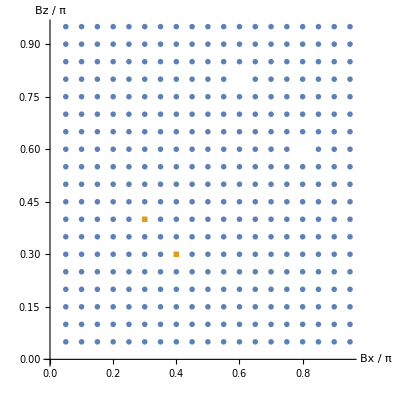

```mathematica
N[Length[NonDecreasingTracePointsBeff]/(Length[NonDecreasingTracePointsBeff]+Length[Det0PointsBeff])]*100
N[Length[Det0PointsBeff]/(Length[NonDecreasingTracePointsBeff]+Length[Det0PointsBeff])]*100
PlotBeff=ListPlot[{NonDecreasingTracePointsBeff,Det0PointsBeff},AspectRatio->1,PlotMarkers->{Automatic,0.05},AxesLabel->{"Bx / π","Bz / π"}]
```

```mathematica
TraceListTotalBeff[[103]]
DetListTotalBeff[[103]]
TraceListTotalBeff[[75]]
DetListTotalBeff[[75]]
TraceListTotalBeff[[70]]
DetListTotalBeff[[70]]
```

{0.3,0.4,{4.69125×10^15,1.40737×10^16,Tr[Inverse[{{0.176659,-0.132494},{-0.132494,0.0993704}}]],-4.5036×10^17,-9.0072×10^17,Tr[Inverse[{{0.00130043,-0.000975324},{-0.000975324,0.000731493}}]],5.76461×10^19,-4.61169×10^20,-1.84467×10^21,1.47574×10^22}}

{0.3,0.4,{5.59314×10^-16,7.64072×10^-17,0.,-1.3001×10^-19,-1.24999×10^-20,0.,6.07505×10^-24,-1.26359×10^-25,-5.11332×10^-27,1.01188×10^-28}}

{0.2,0.9,{1.31746×10^8,8.23895×10^10,6.85893×10^13,Tr[Inverse[{{16.6628,69.0663},{69.0663,286.276}}]],-3.08652×10^14,1.54326×10^14,Tr[Inverse[{{45.5174,188.667},{188.667,782.017}}]],-7.71629×10^13,7.71629×10^13,7.71629×10^13}}

{0.2,0.9,{2.59831×10^-7,1.14777×10^-9,2.6865×10^-12,0.,-1.45822×10^-12,4.05015×10^-12,0.,-1.37003×10^-11,1.70175×10^-11,2.06722×10^-11}}

{0.2,0.65,{13859.7,30253.5,5.40909×10^6,3.82943×10^8,7.15743×10^9,7.84136×10^12,Tr[Inverse[{{45.74,120.213},{120.213,315.942}}]],5.29292×10^13,3.52861×10^13,Tr[Inverse[{{61.2752,161.042},{161.042,423.249}}]]}}

{0.2,0.65,{0.00224637,0.00252655,0.0000242641,4.97272×10^-7,3.50904×10^-8,3.94502×10^-11,0.,7.71614×10^-12,1.27536×10^-11,0.}}

```mathematica
DetListTotalBeff;
```

```mathematica
TraceListTotalBeff;
```

```mathematica
AllTrue[{0,0,0},Abs[#]<10^-12&]
```

True

```mathematica
!OrderedQ[{5,4,3,2},Greater]
```

False

### Combined

```mathematica
(* nmin (nmax) is the smallest (largest) value of N (number of spins) that we consider *)
nmin=3;
nmax=21;

(* minB (maxB) is the smallest (largest) value of B (the magnetic field) that we consider  *)
minB=0.0;
maxB=1.0;

(*  stepB: the difference between each contiguous B values *)
stepB=0.05;


DetListTotalCombined={}; (* list of Det[F] for every magnetic field vector *)
TraceListTotalCombined={}; (* list of Trace[F^{-1}] for every magnetic field vector *)

(* We classify each magnetic field vector in 4 possible sets: *)
IndetPoints={}; (* magnetic field vectors for which Det[F] has Infinite or Indeterminate entries *)
Det0Points={};   (* magnetic field vectors for which Det[F] == 0 *)
NonDecreasingTracePoints={};  (* magnetic field vectors for which Trace[F^{-1}] does not decrease with increasing N (not even shot-noise scaling) *)
DecreasingTracePoints={}; (* magnetic field vectors for which Trace[F^{-1}] decreases with increasing N *)

(* Main loop *)
For[Bxaux=minB+stepB,Bxaux<=maxB-stepB,Bxaux+=stepB,
For[Bzaux=minB+stepB,Bzaux<=maxB-stepB,Bzaux+=stepB,

Print["(Bx, Bz) = (", Bxaux, ", ", Bzaux, ")" ];
Print[DateString[{"Hour",":","Minute",":","Second"}]];


DetListLocal={};
TraceListLocal={};

(* Second for loop over several values of N (number of qubits) *)
For[naux=nmin,naux<=nmax,naux+=2,

FoutcomesQECxxZ=Sum[((1/pkQECfullZ)*D[pkQECfullZ,Bx]*D[pkQECfullZ,Bx])/.{n->naux,Bx->Bxaux*Pi,Bz->Bzaux*Pi},{kx,0,(naux-1)/2}];
FoutcomesQECzzZ=Sum[((1/pkQECfullZ)*D[pkQECfullZ,Bz]*D[pkQECfullZ,Bz])/.{n->naux,Bx->Bxaux*Pi,Bz->Bzaux*Pi},{kx,0,(naux-1)/2}];
FoutcomesQECxzZ=Sum[((1/pkQECfullZ)*D[pkQECfullZ,Bx]*D[pkQECfullZ,Bz])/.{n->naux,Bx->Bxaux*Pi,Bz->Bzaux*Pi},{kx,0,(naux-1)/2}];
FoutcomesQECZ={{FoutcomesQECxxZ,FoutcomesQECxzZ},{FoutcomesQECxzZ,FoutcomesQECzzZ}};

FBeffQECxxZ=Sum[(pkQECfullZ*((1/pplusQECfullZ)*D[pplusQECfullZ,Bx]*D[pplusQECfullZ,Bx]+(1/pminusQECfullZ)*D[pminusQECfullZ,Bx]*D[pminusQECfullZ,Bx]))/.{n->naux,Bx->Bxaux*Pi,Bz->Bzaux*Pi},{kx,0,(naux-1)/2}];
FBeffQECzzZ=Sum[(pkQECfullZ*((1/pplusQECfullZ)*D[pplusQECfullZ,Bz]*D[pplusQECfullZ,Bz]+(1/pminusQECfullZ)*D[pminusQECfullZ,Bz]*D[pminusQECfullZ,Bz]))/.{n->naux,Bx->Bxaux*Pi,Bz->Bzaux*Pi},{kx,0,(naux-1)/2}];
FBeffQECxzZ=Sum[(pkQECfullZ*((1/pplusQECfullZ)*D[pplusQECfullZ,Bx]*D[pplusQECfullZ,Bz]+(1/pminusQECfullZ)*D[pminusQECfullZ,Bx]*D[pminusQECfullZ,Bz]))/.{n->naux,Bx->Bxaux*Pi,Bz->Bzaux*Pi},{kx,0,(naux-1)/2}];
FBeffQECZ={{FBeffQECxxZ,FBeffQECxzZ},{FBeffQECxzZ,FBeffQECzzZ}};

FQECnZ=FoutcomesQECZ+FBeffQECZ;
AppendTo[DetListLocal,Det[FQECnZ]];
AppendTo[TraceListLocal,Tr[Inverse[FQECnZ]]];


];

(* For a given magnetic field vector, we append the resulting local lists to the total lists *)
AppendTo[DetListTotalCombined,{Bxaux,Bzaux,DetListLocal}];
AppendTo[TraceListTotalCombined,{Bxaux,Bzaux,TraceListLocal}];

(* Now we classify the magnetic field vector into 1 of the 4 sets described above *)
cond1=MemberQ[DetListLocal,ComplexInfinity]||MemberQ[DetListLocal,Indeterminate];
If[cond1,
(
AppendTo[IndetPoints,{Bxaux,Bzaux}];
),
(
cond2=AllTrue[DetListLocal,Abs[#]<10^-14&];
If[cond2,
(
AppendTo[Det0Points,{Bxaux,Bzaux}];
),
(
cond3=OrderedQ[TraceListLocal,Greater];
If[cond3,
(
AppendTo[DecreasingTracePoints,{Bxaux,Bzaux}];
),
(
AppendTo[NonDecreasingTracePoints,{Bxaux,Bzaux}];
)
];
)
];
)
];


];
];


(* Folder path where the results will be saved (remember to change this accordingly) *)
folderPath="/home/mauricio/Documents/Research/QEC/QSensing/Results/";

(*Export data*)
Export[FileNameJoin[{folderPath,"DetListTotalCombined.mx"}],DetListTotalCombined];
Export[FileNameJoin[{folderPath,"TraceListTotalCombined.mx"}],TraceListTotalCombined];
Export[FileNameJoin[{folderPath,"IndetPoints.mx"}],IndetPoints];
Export[FileNameJoin[{folderPath,"Det0Points.mx"}],Det0Points];
Export[FileNameJoin[{folderPath,"NonDecreasingTracePoints.mx"}],NonDecreasingTracePoints];
Export[FileNameJoin[{folderPath,"DecreasingTracePoints.mx"}],DecreasingTracePoints];
```

(Bx, Bz) = (0.05, 0.05)

22:19:19

(Bx, Bz) = (0.05, 0.1)

22:19:19

(Bx, Bz) = (0.05, 0.15)

22:19:20

(Bx, Bz) = (0.05, 0.2)

22:19:20

(Bx, Bz) = (0.05, 0.25)

22:19:20

(Bx, Bz) = (0.05, 0.3)

22:19:21

(Bx, Bz) = (0.05, 0.35)

22:19:21

(Bx, Bz) = (0.05, 0.4)

22:19:21

(Bx, Bz) = (0.05, 0.45)

22:19:22

(Bx, Bz) = (0.05, 0.5)

22:19:22

(Bx, Bz) = (0.05, 0.55)

22:19:22

(Bx, Bz) = (0.05, 0.6)

22:19:23

(Bx, Bz) = (0.05, 0.65)

22:19:23

(Bx, Bz) = (0.05, 0.7)

22:19:23

(Bx, Bz) = (0.05, 0.75)

22:19:24

(Bx, Bz) = (0.05, 0.8)

22:19:24

(Bx, Bz) = (0.05, 0.85)

22:19:25

(Bx, Bz) = (0.05, 0.9)

22:19:25

(Bx, Bz) = (0.05, 0.95)

22:19:25

(Bx, Bz) = (0.1, 0.05)

22:19:26

(Bx, Bz) = (0.1, 0.1)

22:19:26

(Bx, Bz) = (0.1, 0.15)

22:19:26

(Bx, Bz) = (0.1, 0.2)

22:19:27

(Bx, Bz) = (0.1, 0.25)

22:19:27

(Bx, Bz) = (0.1, 0.3)

22:19:27

(Bx, Bz) = (0.1, 0.35)

22:19:28

(Bx, Bz) = (0.1, 0.4)

22:19:28

(Bx, Bz) = (0.1, 0.45)

22:19:28

(Bx, Bz) = (0.1, 0.5)

22:19:29

(Bx, Bz) = (0.1, 0.55)

22:19:29

(Bx, Bz) = (0.1, 0.6)

22:19:29

(Bx, Bz) = (0.1, 0.65)

22:19:30

(Bx, Bz) = (0.1, 0.7)

22:19:30

(Bx, Bz) = (0.1, 0.75)

22:19:31

(Bx, Bz) = (0.1, 0.8)

22:19:31

(Bx, Bz) = (0.1, 0.85)

22:19:31

(Bx, Bz) = (0.1, 0.9)

22:19:32

(Bx, Bz) = (0.1, 0.95)

22:19:32

(Bx, Bz) = (0.15, 0.05)

22:19:32

(Bx, Bz) = (0.15, 0.1)

22:19:33

(Bx, Bz) = (0.15, 0.15)

22:19:33

(Bx, Bz) = (0.15, 0.2)

22:19:33

(Bx, Bz) = (0.15, 0.25)

22:19:34

(Bx, Bz) = (0.15, 0.3)

22:19:34

(Bx, Bz) = (0.15, 0.35)

22:19:34

(Bx, Bz) = (0.15, 0.4)

22:19:35

(Bx, Bz) = (0.15, 0.45)

22:19:35

(Bx, Bz) = (0.15, 0.5)

22:19:35

(Bx, Bz) = (0.15, 0.55)

22:19:36

(Bx, Bz) = (0.15, 0.6)

22:19:36

(Bx, Bz) = (0.15, 0.65)

22:19:37

(Bx, Bz) = (0.15, 0.7)

22:19:37

(Bx, Bz) = (0.15, 0.75)

22:19:37

(Bx, Bz) = (0.15, 0.8)

22:19:38

(Bx, Bz) = (0.15, 0.85)

22:19:38

(Bx, Bz) = (0.15, 0.9)

22:19:38

(Bx, Bz) = (0.15, 0.95)

22:19:39

(Bx, Bz) = (0.2, 0.05)

22:19:39

(Bx, Bz) = (0.2, 0.1)

22:19:39

(Bx, Bz) = (0.2, 0.15)

22:19:40

(Bx, Bz) = (0.2, 0.2)

22:19:40

(Bx, Bz) = (0.2, 0.25)

22:19:40

(Bx, Bz) = (0.2, 0.3)

22:19:41

(Bx, Bz) = (0.2, 0.35)

22:19:41

(Bx, Bz) = (0.2, 0.4)

22:19:41

(Bx, Bz) = (0.2, 0.45)

22:19:42

(Bx, Bz) = (0.2, 0.5)

22:19:42

(Bx, Bz) = (0.2, 0.55)

22:19:43

(Bx, Bz) = (0.2, 0.6)

22:19:43

(Bx, Bz) = (0.2, 0.65)

22:19:43

(Bx, Bz) = (0.2, 0.7)

22:19:44

(Bx, Bz) = (0.2, 0.75)

22:19:44

(Bx, Bz) = (0.2, 0.8)

22:19:44

(Bx, Bz) = (0.2, 0.85)

22:19:45

(Bx, Bz) = (0.2, 0.9)

22:19:45

(Bx, Bz) = (0.2, 0.95)

22:19:45

(Bx, Bz) = (0.25, 0.05)

22:19:46

(Bx, Bz) = (0.25, 0.1)

22:19:46

(Bx, Bz) = (0.25, 0.15)

22:19:46

(Bx, Bz) = (0.25, 0.2)

22:19:47

(Bx, Bz) = (0.25, 0.25)

22:19:47

(Bx, Bz) = (0.25, 0.3)

22:19:47

(Bx, Bz) = (0.25, 0.35)

22:19:48

(Bx, Bz) = (0.25, 0.4)

22:19:48

(Bx, Bz) = (0.25, 0.45)

22:19:49

(Bx, Bz) = (0.25, 0.5)

22:19:49

(Bx, Bz) = (0.25, 0.55)

22:19:49

(Bx, Bz) = (0.25, 0.6)

22:19:50

(Bx, Bz) = (0.25, 0.65)

22:19:50

(Bx, Bz) = (0.25, 0.7)

22:19:50

(Bx, Bz) = (0.25, 0.75)

22:19:51

(Bx, Bz) = (0.25, 0.8)

22:19:51

(Bx, Bz) = (0.25, 0.85)

22:19:51

(Bx, Bz) = (0.25, 0.9)

22:19:52

(Bx, Bz) = (0.25, 0.95)

22:19:52

(Bx, Bz) = (0.3, 0.05)

22:19:52

(Bx, Bz) = (0.3, 0.1)

22:19:53

(Bx, Bz) = (0.3, 0.15)

22:19:53

(Bx, Bz) = (0.3, 0.2)

22:19:53

(Bx, Bz) = (0.3, 0.25)

22:19:54

(Bx, Bz) = (0.3, 0.3)

22:19:54

(Bx, Bz) = (0.3, 0.35)

22:19:55

(Bx, Bz) = (0.3, 0.4)

22:19:55

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.46953,-1.85215},{-1.85215,1.38911}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.83147,-2.1236},{-2.1236,1.5927}} may contain significant numerical errors.

Inverse::sing: Matrix {{3.99657,-2.99743},{-2.99743,2.24807}} is singular.

Inverse::luc: Result for Inverse of badly conditioned matrix {{5.73707,-4.3028},{-4.3028,3.2271}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::sing: Matrix {{7.71909,-5.78931},{-5.78931,4.34199}} is singular.

Inverse::sing: Matrix {{11.9717,-8.9788},{-8.9788,6.7341}} is singular.

General::stop: Further output of Inverse::sing will be suppressed during this calculation.

(Bx, Bz) = (0.3, 0.45)

22:19:55

(Bx, Bz) = (0.3, 0.5)

22:19:56

(Bx, Bz) = (0.3, 0.55)

22:19:56

(Bx, Bz) = (0.3, 0.6)

22:19:57

(Bx, Bz) = (0.3, 0.65)

22:19:57

(Bx, Bz) = (0.3, 0.7)

22:19:57

(Bx, Bz) = (0.3, 0.75)

22:19:58

(Bx, Bz) = (0.3, 0.8)

22:19:58

(Bx, Bz) = (0.3, 0.85)

22:19:58

(Bx, Bz) = (0.3, 0.9)

22:19:59

(Bx, Bz) = (0.3, 0.95)

22:19:59

(Bx, Bz) = (0.35, 0.05)

22:19:59

(Bx, Bz) = (0.35, 0.1)

22:20:00

(Bx, Bz) = (0.35, 0.15)

22:20:00

(Bx, Bz) = (0.35, 0.2)

22:20:00

(Bx, Bz) = (0.35, 0.25)

22:20:01

(Bx, Bz) = (0.35, 0.3)

22:20:01

(Bx, Bz) = (0.35, 0.35)

22:20:01

(Bx, Bz) = (0.35, 0.4)

22:20:02

(Bx, Bz) = (0.35, 0.45)

22:20:02

(Bx, Bz) = (0.35, 0.5)

22:20:03

(Bx, Bz) = (0.35, 0.55)

22:20:03

(Bx, Bz) = (0.35, 0.6)

22:20:03

(Bx, Bz) = (0.35, 0.65)

22:20:04

(Bx, Bz) = (0.35, 0.7)

22:20:04

(Bx, Bz) = (0.35, 0.75)

22:20:04

(Bx, Bz) = (0.35, 0.8)

22:20:05

(Bx, Bz) = (0.35, 0.85)

22:20:05

(Bx, Bz) = (0.35, 0.9)

22:20:05

(Bx, Bz) = (0.35, 0.95)

22:20:06

(Bx, Bz) = (0.4, 0.05)

22:20:06

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Det::mindet: Input matrix contains an indeterminate entry.

Inverse::mindet: Input matrix contains an indeterminate entry.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Det::mindet: Input matrix contains an indeterminate entry.

Inverse::mindet: Input matrix contains an indeterminate entry.

Det::inf: Input matrix contains an infinite entry.

Inverse::inf: Input matrix contains an infinite entry.

(Bx, Bz) = (0.4, 0.1)

22:20:06

(Bx, Bz) = (0.4, 0.15)

22:20:07

(Bx, Bz) = (0.4, 0.2)

22:20:07

(Bx, Bz) = (0.4, 0.25)

22:20:08

(Bx, Bz) = (0.4, 0.3)

22:20:08

(Bx, Bz) = (0.4, 0.35)

22:20:08

(Bx, Bz) = (0.4, 0.4)

22:20:09

(Bx, Bz) = (0.4, 0.45)

22:20:09

(Bx, Bz) = (0.4, 0.5)

22:20:09

(Bx, Bz) = (0.4, 0.55)

22:20:10

(Bx, Bz) = (0.4, 0.6)

22:20:10

(Bx, Bz) = (0.4, 0.65)

22:20:11

(Bx, Bz) = (0.4, 0.7)

22:20:11

(Bx, Bz) = (0.4, 0.75)

22:20:11

(Bx, Bz) = (0.4, 0.8)

22:20:12

(Bx, Bz) = (0.4, 0.85)

22:20:12

(Bx, Bz) = (0.4, 0.9)

22:20:12

(Bx, Bz) = (0.4, 0.95)

22:20:13

(Bx, Bz) = (0.45, 0.05)

22:20:13

Det::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Det::mindet will be suppressed during this calculation.

Inverse::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Inverse::mindet will be suppressed during this calculation.

Det::inf: Input matrix contains an infinite entry.

Inverse::inf: Input matrix contains an infinite entry.

(Bx, Bz) = (0.45, 0.1)

22:20:13

Det::inf: Input matrix contains an infinite entry.

General::stop: Further output of Det::inf will be suppressed during this calculation.

Inverse::inf: Input matrix contains an infinite entry.

General::stop: Further output of Inverse::inf will be suppressed during this calculation.

(Bx, Bz) = (0.45, 0.15)

22:20:14

(Bx, Bz) = (0.45, 0.2)

22:20:14

(Bx, Bz) = (0.45, 0.25)

22:20:14

(Bx, Bz) = (0.45, 0.3)

22:20:15

(Bx, Bz) = (0.45, 0.35)

22:20:15

(Bx, Bz) = (0.45, 0.4)

22:20:15

(Bx, Bz) = (0.45, 0.45)

22:20:16

(Bx, Bz) = (0.45, 0.5)

22:20:16

(Bx, Bz) = (0.45, 0.55)

22:20:17

(Bx, Bz) = (0.45, 0.6)

22:20:17

(Bx, Bz) = (0.45, 0.65)

22:20:17

(Bx, Bz) = (0.45, 0.7)

22:20:18

(Bx, Bz) = (0.45, 0.75)

22:20:18

(Bx, Bz) = (0.45, 0.8)

22:20:18

(Bx, Bz) = (0.45, 0.85)

22:20:19

(Bx, Bz) = (0.45, 0.9)

22:20:19

(Bx, Bz) = (0.45, 0.95)

22:20:19

(Bx, Bz) = (0.5, 0.05)

22:20:20

(Bx, Bz) = (0.5, 0.1)

22:20:20

(Bx, Bz) = (0.5, 0.15)

22:20:20

(Bx, Bz) = (0.5, 0.2)

22:20:21

(Bx, Bz) = (0.5, 0.25)

22:20:21

(Bx, Bz) = (0.5, 0.3)

22:20:21

(Bx, Bz) = (0.5, 0.35)

22:20:22

(Bx, Bz) = (0.5, 0.4)

22:20:22

(Bx, Bz) = (0.5, 0.45)

22:20:23

(Bx, Bz) = (0.5, 0.5)

22:20:23

(Bx, Bz) = (0.5, 0.55)

22:20:23

(Bx, Bz) = (0.5, 0.6)

22:20:24

(Bx, Bz) = (0.5, 0.65)

22:20:24

(Bx, Bz) = (0.5, 0.7)

22:20:24

(Bx, Bz) = (0.5, 0.75)

22:20:25

(Bx, Bz) = (0.5, 0.8)

22:20:25

(Bx, Bz) = (0.5, 0.85)

22:20:25

(Bx, Bz) = (0.5, 0.9)

22:20:26

(Bx, Bz) = (0.5, 0.95)

22:20:26

(Bx, Bz) = (0.55, 0.05)

22:20:26

(Bx, Bz) = (0.55, 0.1)

22:20:27

(Bx, Bz) = (0.55, 0.15)

22:20:27

(Bx, Bz) = (0.55, 0.2)

22:20:28

(Bx, Bz) = (0.55, 0.25)

22:20:28

(Bx, Bz) = (0.55, 0.3)

22:20:28

(Bx, Bz) = (0.55, 0.35)

22:20:29

(Bx, Bz) = (0.55, 0.4)

22:20:29

(Bx, Bz) = (0.55, 0.45)

22:20:29

(Bx, Bz) = (0.55, 0.5)

22:20:30

(Bx, Bz) = (0.55, 0.55)

22:20:30

(Bx, Bz) = (0.55, 0.6)

22:20:30

(Bx, Bz) = (0.55, 0.65)

22:20:31

(Bx, Bz) = (0.55, 0.7)

22:20:31

(Bx, Bz) = (0.55, 0.75)

22:20:31

(Bx, Bz) = (0.55, 0.8)

22:20:32

(Bx, Bz) = (0.55, 0.85)

22:20:32

(Bx, Bz) = (0.55, 0.9)

22:20:32

(Bx, Bz) = (0.55, 0.95)

22:20:33

(Bx, Bz) = (0.6, 0.05)

22:20:33

(Bx, Bz) = (0.6, 0.1)

22:20:34

(Bx, Bz) = (0.6, 0.15)

22:20:34

(Bx, Bz) = (0.6, 0.2)

22:20:34

(Bx, Bz) = (0.6, 0.25)

22:20:35

(Bx, Bz) = (0.6, 0.3)

22:20:35

(Bx, Bz) = (0.6, 0.35)

22:20:35

(Bx, Bz) = (0.6, 0.4)

22:20:36

(Bx, Bz) = (0.6, 0.45)

22:20:36

(Bx, Bz) = (0.6, 0.5)

22:20:36

(Bx, Bz) = (0.6, 0.55)

22:20:37

(Bx, Bz) = (0.6, 0.6)

22:20:37

(Bx, Bz) = (0.6, 0.65)

22:20:37

(Bx, Bz) = (0.6, 0.7)

22:20:38

(Bx, Bz) = (0.6, 0.75)

22:20:38

(Bx, Bz) = (0.6, 0.8)

22:20:38

General::munfl: (-1.92975×10^-16)^21 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.92975×10^-16)^22 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.92975×10^-16)^20 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Divide::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

(Bx, Bz) = (0.6, 0.85)

22:20:39

(Bx, Bz) = (0.6, 0.9)

22:20:39

(Bx, Bz) = (0.6, 0.95)

22:20:40

(Bx, Bz) = (0.65, 0.05)

22:20:40

(Bx, Bz) = (0.65, 0.1)

22:20:40

(Bx, Bz) = (0.65, 0.15)

22:20:41

(Bx, Bz) = (0.65, 0.2)

22:20:41

(Bx, Bz) = (0.65, 0.25)

22:20:42

(Bx, Bz) = (0.65, 0.3)

22:20:42

(Bx, Bz) = (0.65, 0.35)

22:20:42

(Bx, Bz) = (0.65, 0.4)

22:20:43

(Bx, Bz) = (0.65, 0.45)

22:20:43

(Bx, Bz) = (0.65, 0.5)

22:20:43

(Bx, Bz) = (0.65, 0.55)

22:20:44

(Bx, Bz) = (0.65, 0.6)

22:20:44

(Bx, Bz) = (0.65, 0.65)

22:20:44

(Bx, Bz) = (0.65, 0.7)

22:20:45

(Bx, Bz) = (0.65, 0.75)

22:20:45

(Bx, Bz) = (0.65, 0.8)

22:20:45

(Bx, Bz) = (0.65, 0.85)

22:20:46

(Bx, Bz) = (0.65, 0.9)

22:20:46

(Bx, Bz) = (0.65, 0.95)

22:20:47

(Bx, Bz) = (0.7, 0.05)

22:20:47

(Bx, Bz) = (0.7, 0.1)

22:20:47

(Bx, Bz) = (0.7, 0.15)

22:20:48

(Bx, Bz) = (0.7, 0.2)

22:20:48

(Bx, Bz) = (0.7, 0.25)

22:20:48

(Bx, Bz) = (0.7, 0.3)

22:20:49

(Bx, Bz) = (0.7, 0.35)

22:20:49

(Bx, Bz) = (0.7, 0.4)

22:20:49

(Bx, Bz) = (0.7, 0.45)

22:20:50

(Bx, Bz) = (0.7, 0.5)

22:20:50

(Bx, Bz) = (0.7, 0.55)

22:20:50

(Bx, Bz) = (0.7, 0.6)

22:20:51

(Bx, Bz) = (0.7, 0.65)

22:20:51

(Bx, Bz) = (0.7, 0.7)

22:20:51

(Bx, Bz) = (0.7, 0.75)

22:20:52

(Bx, Bz) = (0.7, 0.8)

22:20:52

(Bx, Bz) = (0.7, 0.85)

22:20:53

(Bx, Bz) = (0.7, 0.9)

22:20:53

(Bx, Bz) = (0.7, 0.95)

22:20:53

(Bx, Bz) = (0.75, 0.05)

22:20:54

(Bx, Bz) = (0.75, 0.1)

22:20:54

(Bx, Bz) = (0.75, 0.15)

22:20:54

(Bx, Bz) = (0.75, 0.2)

22:20:55

(Bx, Bz) = (0.75, 0.25)

22:20:55

(Bx, Bz) = (0.75, 0.3)

22:20:55

(Bx, Bz) = (0.75, 0.35)

22:20:56

(Bx, Bz) = (0.75, 0.4)

22:20:56

(Bx, Bz) = (0.75, 0.45)

22:20:56

(Bx, Bz) = (0.75, 0.5)

22:20:57

(Bx, Bz) = (0.75, 0.55)

22:20:57

(Bx, Bz) = (0.75, 0.6)

22:20:57

(Bx, Bz) = (0.75, 0.65)

22:20:58

(Bx, Bz) = (0.75, 0.7)

22:20:58

(Bx, Bz) = (0.75, 0.75)

22:20:59

(Bx, Bz) = (0.75, 0.8)

22:20:59

(Bx, Bz) = (0.75, 0.85)

22:20:59

(Bx, Bz) = (0.75, 0.9)

22:21:00

(Bx, Bz) = (0.75, 0.95)

22:21:00

(Bx, Bz) = (0.8, 0.05)

22:21:00

(Bx, Bz) = (0.8, 0.1)

22:21:01

(Bx, Bz) = (0.8, 0.15)

22:21:01

(Bx, Bz) = (0.8, 0.2)

22:21:01

(Bx, Bz) = (0.8, 0.25)

22:21:02

(Bx, Bz) = (0.8, 0.3)

22:21:02

(Bx, Bz) = (0.8, 0.35)

22:21:02

(Bx, Bz) = (0.8, 0.4)

22:21:03

(Bx, Bz) = (0.8, 0.45)

22:21:03

(Bx, Bz) = (0.8, 0.5)

22:21:03

(Bx, Bz) = (0.8, 0.55)

22:21:04

(Bx, Bz) = (0.8, 0.6)

22:21:04

(Bx, Bz) = (0.8, 0.65)

22:21:05

(Bx, Bz) = (0.8, 0.7)

22:21:05

(Bx, Bz) = (0.8, 0.75)

22:21:05

(Bx, Bz) = (0.8, 0.8)

22:21:06

(Bx, Bz) = (0.8, 0.85)

22:21:06

(Bx, Bz) = (0.8, 0.9)

22:21:07

(Bx, Bz) = (0.8, 0.95)

22:21:07

(Bx, Bz) = (0.85, 0.05)

22:21:07

(Bx, Bz) = (0.85, 0.1)

22:21:08

(Bx, Bz) = (0.85, 0.15)

22:21:08

(Bx, Bz) = (0.85, 0.2)

22:21:08

(Bx, Bz) = (0.85, 0.25)

22:21:09

(Bx, Bz) = (0.85, 0.3)

22:21:09

(Bx, Bz) = (0.85, 0.35)

22:21:09

(Bx, Bz) = (0.85, 0.4)

22:21:10

(Bx, Bz) = (0.85, 0.45)

22:21:10

(Bx, Bz) = (0.85, 0.5)

22:21:10

(Bx, Bz) = (0.85, 0.55)

22:21:11

(Bx, Bz) = (0.85, 0.6)

22:21:11

(Bx, Bz) = (0.85, 0.65)

22:21:11

(Bx, Bz) = (0.85, 0.7)

22:21:12

(Bx, Bz) = (0.85, 0.75)

22:21:12

(Bx, Bz) = (0.85, 0.8)

22:21:13

(Bx, Bz) = (0.85, 0.85)

22:21:13

(Bx, Bz) = (0.85, 0.9)

22:21:13

(Bx, Bz) = (0.85, 0.95)

22:21:14

(Bx, Bz) = (0.9, 0.05)

22:21:14

(Bx, Bz) = (0.9, 0.1)

22:21:14

(Bx, Bz) = (0.9, 0.15)

22:21:15

(Bx, Bz) = (0.9, 0.2)

22:21:15

(Bx, Bz) = (0.9, 0.25)

22:21:15

(Bx, Bz) = (0.9, 0.3)

22:21:16

(Bx, Bz) = (0.9, 0.35)

22:21:16

(Bx, Bz) = (0.9, 0.4)

22:21:16

(Bx, Bz) = (0.9, 0.45)

22:21:17

(Bx, Bz) = (0.9, 0.5)

22:21:17

(Bx, Bz) = (0.9, 0.55)

22:21:17

(Bx, Bz) = (0.9, 0.6)

22:21:18

(Bx, Bz) = (0.9, 0.65)

22:21:18

(Bx, Bz) = (0.9, 0.7)

22:21:18

(Bx, Bz) = (0.9, 0.75)

22:21:19

(Bx, Bz) = (0.9, 0.8)

22:21:19

(Bx, Bz) = (0.9, 0.85)

22:21:20

(Bx, Bz) = (0.9, 0.9)

22:21:20

(Bx, Bz) = (0.9, 0.95)

22:21:20

(Bx, Bz) = (0.95, 0.05)

22:21:21

(Bx, Bz) = (0.95, 0.1)

22:21:21

(Bx, Bz) = (0.95, 0.15)

22:21:21

(Bx, Bz) = (0.95, 0.2)

22:21:22

(Bx, Bz) = (0.95, 0.25)

22:21:22

(Bx, Bz) = (0.95, 0.3)

22:21:22

(Bx, Bz) = (0.95, 0.35)

22:21:23

(Bx, Bz) = (0.95, 0.4)

22:21:23

(Bx, Bz) = (0.95, 0.45)

22:21:23

(Bx, Bz) = (0.95, 0.5)

22:21:24

(Bx, Bz) = (0.95, 0.55)

22:21:24

(Bx, Bz) = (0.95, 0.6)

22:21:24

(Bx, Bz) = (0.95, 0.65)

22:21:25

(Bx, Bz) = (0.95, 0.7)

22:21:25

(Bx, Bz) = (0.95, 0.75)

22:21:25

(Bx, Bz) = (0.95, 0.8)

22:21:26

(Bx, Bz) = (0.95, 0.85)

22:21:26

(Bx, Bz) = (0.95, 0.9)

22:21:27

(Bx, Bz) = (0.95, 0.95)

22:21:27

```mathematica
IndetPoints
Det0Points
NonDecreasingTracePoints
DecreasingTracePoints
```

{}

{}

{{0.15,0.05},{0.15,0.1},{0.15,0.15},{0.15,0.2},{0.15,0.25},{0.15,0.3},{0.2,0.05},{0.2,0.1},{0.2,0.15},{0.2,0.2},{0.2,0.25},{0.2,0.3},{0.2,0.35},{0.2,0.4},{0.2,0.45},{0.25,0.05},{0.25,0.1},{0.25,0.15},{0.25,0.2},{0.25,0.25},{0.25,0.3},{0.25,0.35},{0.25,0.4},{0.25,0.45},{0.25,0.5},{0.3,0.05},{0.3,0.1},{0.3,0.15},{0.3,0.2},{0.3,0.25},{0.3,0.3},{0.3,0.35},{0.3,0.4},{0.3,0.45},{0.3,0.5},{0.3,0.55},{0.35,0.05},{0.35,0.1},{0.35,0.15},{0.35,0.2},{0.35,0.25},{0.35,0.3},{0.35,0.4},{0.35,0.45},{0.35,0.5},{0.35,0.55},{0.4,0.05},{0.4,0.1},{0.4,0.15},{0.4,0.2},{0.4,0.25},{0.4,0.3},{0.4,0.35},{0.4,0.4},{0.4,0.45},{0.4,0.5},{0.4,0.55},{0.4,0.6},{0.45,0.05},{0.45,0.1},{0.45,0.15},{0.45,0.2},{0.45,0.25},{0.45,0.3},{0.45,0.35},{0.45,0.4},{0.45,0.45},{0.45,0.5},{0.45,0.55},{0.45,0.6},{0.5,0.05},{0.5,0.1},{0.5,0.15},{0.5,0.2},{0.5,0.25},{0.5,0.3},{0.5,0.35},{0.5,0.4},{0.5,0.45},{0.5,0.5},{0.5,0.55},{0.5,0.6},{0.55,0.05},{0.55,0.1},{0.55,0.15},{0.55,0.2},{0.55,0.25},{0.55,0.3},{0.55,0.35},{0.55,0.4},{0.55,0.45},{0.55,0.5},{0.55,0.55},{0.6,0.05},{0.6,0.1},{0.6,0.15},{0.6,0.2},{0.6,0.25},{0.6,0.3},{0.6,0.35},{0.6,0.4},{0.6,0.45},{0.6,0.5},{0.6,0.55},{0.65,0.05},{0.65,0.1},{0.65,0.15},{0.65,0.2},{0.65,0.25},{0.65,0.3},{0.65,0.35},{0.65,0.4},{0.65,0.45},{0.65,0.5},{0.65,0.55},{0.7,0.05},{0.7,0.1},{0.7,0.15},{0.7,0.2},{0.7,0.25},{0.7,0.3},{0.7,0.35},{0.7,0.4},{0.7,0.45},{0.75,0.05},{0.75,0.1},{0.75,0.15},{0.75,0.2},{0.75,0.25},{0.75,0.3},{0.75,0.35},{0.75,0.4},{0.8,0.05},{0.8,0.1},{0.8,0.15},{0.8,0.2},{0.8,0.25},{0.8,0.3},{0.8,0.35},{0.8,0.95},{0.85,0.05},{0.85,0.1},{0.85,0.15},{0.85,0.2},{0.85,0.25},{0.85,0.85},{0.85,0.9},{0.85,0.95},{0.9,0.75},{0.9,0.8},{0.9,0.85},{0.9,0.9},{0.9,0.95},{0.95,0.65},{0.95,0.7},{0.95,0.75},{0.95,0.8},{0.95,0.85},{0.95,0.9},{0.95,0.95}}

{{0.05,0.05},{0.05,0.1},{0.05,0.15},{0.05,0.2},{0.05,0.25},{0.05,0.3},{0.05,0.35},{0.05,0.4},{0.05,0.45},{0.05,0.5},{0.05,0.55},{0.05,0.6},{0.05,0.65},{0.05,0.7},{0.05,0.75},{0.05,0.8},{0.05,0.85},{0.05,0.9},{0.05,0.95},{0.1,0.05},{0.1,0.1},{0.1,0.15},{0.1,0.2},{0.1,0.25},{0.1,0.3},{0.1,0.35},{0.1,0.4},{0.1,0.45},{0.1,0.5},{0.1,0.55},{0.1,0.6},{0.1,0.65},{0.1,0.7},{0.1,0.75},{0.1,0.8},{0.1,0.85},{0.1,0.9},{0.1,0.95},{0.15,0.35},{0.15,0.4},{0.15,0.45},{0.15,0.5},{0.15,0.55},{0.15,0.6},{0.15,0.65},{0.15,0.7},{0.15,0.75},{0.15,0.8},{0.15,0.85},{0.15,0.9},{0.15,0.95},{0.2,0.5},{0.2,0.55},{0.2,0.6},{0.2,0.65},{0.2,0.7},{0.2,0.75},{0.2,0.8},{0.2,0.85},{0.2,0.9},{0.2,0.95},{0.25,0.55},{0.25,0.6},{0.25,0.65},{0.25,0.7},{0.25,0.75},{0.25,0.8},{0.25,0.85},{0.25,0.9},{0.25,0.95},{0.3,0.6},{0.3,0.65},{0.3,0.7},{0.3,0.75},{0.3,0.8},{0.3,0.85},{0.3,0.9},{0.3,0.95},{0.35,0.35},{0.35,0.6},{0.35,0.65},{0.35,0.7},{0.35,0.75},{0.35,0.8},{0.35,0.85},{0.35,0.9},{0.35,0.95},{0.4,0.65},{0.4,0.7},{0.4,0.75},{0.4,0.8},{0.4,0.85},{0.4,0.9},{0.4,0.95},{0.45,0.65},{0.45,0.7},{0.45,0.75},{0.45,0.8},{0.45,0.85},{0.45,0.9},{0.45,0.95},{0.5,0.65},{0.5,0.7},{0.5,0.75},{0.5,0.8},{0.5,0.85},{0.5,0.9},{0.5,0.95},{0.55,0.6},{0.55,0.65},{0.55,0.7},{0.55,0.75},{0.55,0.8},{0.55,0.85},{0.55,0.9},{0.55,0.95},{0.6,0.6},{0.6,0.65},{0.6,0.7},{0.6,0.75},{0.6,0.85},{0.6,0.9},{0.6,0.95},{0.65,0.6},{0.65,0.65},{0.65,0.7},{0.65,0.75},{0.65,0.8},{0.65,0.85},{0.65,0.9},{0.65,0.95},{0.7,0.5},{0.7,0.55},{0.7,0.6},{0.7,0.65},{0.7,0.7},{0.7,0.75},{0.7,0.8},{0.7,0.85},{0.7,0.9},{0.7,0.95},{0.75,0.45},{0.75,0.5},{0.75,0.55},{0.75,0.6},{0.75,0.65},{0.75,0.7},{0.75,0.75},{0.75,0.8},{0.75,0.85},{0.75,0.9},{0.75,0.95},{0.8,0.4},{0.8,0.45},{0.8,0.5},{0.8,0.55},{0.8,0.65},{0.8,0.7},{0.8,0.75},{0.8,0.8},{0.8,0.85},{0.8,0.9},{0.85,0.3},{0.85,0.35},{0.85,0.4},{0.85,0.45},{0.85,0.5},{0.85,0.55},{0.85,0.6},{0.85,0.65},{0.85,0.7},{0.85,0.75},{0.85,0.8},{0.9,0.05},{0.9,0.1},{0.9,0.15},{0.9,0.2},{0.9,0.25},{0.9,0.3},{0.9,0.35},{0.9,0.4},{0.9,0.45},{0.9,0.5},{0.9,0.55},{0.9,0.6},{0.9,0.65},{0.9,0.7},{0.95,0.05},{0.95,0.1},{0.95,0.15},{0.95,0.2},{0.95,0.25},{0.95,0.3},{0.95,0.35},{0.95,0.4},{0.95,0.45},{0.95,0.5},{0.95,0.55},{0.95,0.6}}

```mathematica
IndetPoints
Det0Points
NonDecreasingTracePoints
DecreasingTracePoints
```

{}

{}

{{0.15,0.05},{0.15,0.1},{0.15,0.15},{0.15,0.2},{0.15,0.25},{0.15,0.3},{0.2,0.05},{0.2,0.1},{0.2,0.15},{0.2,0.2},{0.2,0.25},{0.2,0.3},{0.2,0.35},{0.2,0.4},{0.2,0.45},{0.25,0.05},{0.25,0.1},{0.25,0.15},{0.25,0.2},{0.25,0.25},{0.25,0.3},{0.25,0.35},{0.25,0.4},{0.25,0.45},{0.25,0.5},{0.3,0.05},{0.3,0.1},{0.3,0.15},{0.3,0.2},{0.3,0.25},{0.3,0.3},{0.3,0.35},{0.3,0.4},{0.3,0.45},{0.3,0.5},{0.3,0.55},{0.35,0.05},{0.35,0.1},{0.35,0.15},{0.35,0.2},{0.35,0.25},{0.35,0.3},{0.35,0.4},{0.35,0.45},{0.35,0.5},{0.35,0.55},{0.4,0.05},{0.4,0.1},{0.4,0.15},{0.4,0.2},{0.4,0.25},{0.4,0.3},{0.4,0.35},{0.4,0.4},{0.4,0.45},{0.4,0.5},{0.4,0.55},{0.4,0.6},{0.45,0.05},{0.45,0.1},{0.45,0.15},{0.45,0.2},{0.45,0.25},{0.45,0.3},{0.45,0.35},{0.45,0.4},{0.45,0.45},{0.45,0.5},{0.45,0.55},{0.45,0.6},{0.5,0.05},{0.5,0.1},{0.5,0.15},{0.5,0.2},{0.5,0.25},{0.5,0.3},{0.5,0.35},{0.5,0.4},{0.5,0.45},{0.5,0.5},{0.5,0.55},{0.5,0.6},{0.55,0.05},{0.55,0.1},{0.55,0.15},{0.55,0.2},{0.55,0.25},{0.55,0.3},{0.55,0.35},{0.55,0.4},{0.55,0.45},{0.55,0.5},{0.55,0.55},{0.6,0.05},{0.6,0.1},{0.6,0.15},{0.6,0.2},{0.6,0.25},{0.6,0.3},{0.6,0.35},{0.6,0.4},{0.6,0.45},{0.6,0.5},{0.6,0.55},{0.65,0.05},{0.65,0.1},{0.65,0.15},{0.65,0.2},{0.65,0.25},{0.65,0.3},{0.65,0.35},{0.65,0.4},{0.65,0.45},{0.65,0.5},{0.65,0.55},{0.7,0.05},{0.7,0.1},{0.7,0.15},{0.7,0.2},{0.7,0.25},{0.7,0.3},{0.7,0.35},{0.7,0.4},{0.7,0.45},{0.75,0.05},{0.75,0.1},{0.75,0.15},{0.75,0.2},{0.75,0.25},{0.75,0.3},{0.75,0.35},{0.75,0.4},{0.8,0.05},{0.8,0.1},{0.8,0.15},{0.8,0.2},{0.8,0.25},{0.8,0.3},{0.8,0.35},{0.8,0.95},{0.85,0.05},{0.85,0.1},{0.85,0.15},{0.85,0.2},{0.85,0.25},{0.85,0.85},{0.85,0.9},{0.85,0.95},{0.9,0.75},{0.9,0.8},{0.9,0.85},{0.9,0.9},{0.9,0.95},{0.95,0.65},{0.95,0.7},{0.95,0.75},{0.95,0.8},{0.95,0.85},{0.95,0.9},{0.95,0.95}}

{{0.05,0.05},{0.05,0.1},{0.05,0.15},{0.05,0.2},{0.05,0.25},{0.05,0.3},{0.05,0.35},{0.05,0.4},{0.05,0.45},{0.05,0.5},{0.05,0.55},{0.05,0.6},{0.05,0.65},{0.05,0.7},{0.05,0.75},{0.05,0.8},{0.05,0.85},{0.05,0.9},{0.05,0.95},{0.1,0.05},{0.1,0.1},{0.1,0.15},{0.1,0.2},{0.1,0.25},{0.1,0.3},{0.1,0.35},{0.1,0.4},{0.1,0.45},{0.1,0.5},{0.1,0.55},{0.1,0.6},{0.1,0.65},{0.1,0.7},{0.1,0.75},{0.1,0.8},{0.1,0.85},{0.1,0.9},{0.1,0.95},{0.15,0.35},{0.15,0.4},{0.15,0.45},{0.15,0.5},{0.15,0.55},{0.15,0.6},{0.15,0.65},{0.15,0.7},{0.15,0.75},{0.15,0.8},{0.15,0.85},{0.15,0.9},{0.15,0.95},{0.2,0.5},{0.2,0.55},{0.2,0.6},{0.2,0.65},{0.2,0.7},{0.2,0.75},{0.2,0.8},{0.2,0.85},{0.2,0.9},{0.2,0.95},{0.25,0.55},{0.25,0.6},{0.25,0.65},{0.25,0.7},{0.25,0.75},{0.25,0.8},{0.25,0.85},{0.25,0.9},{0.25,0.95},{0.3,0.6},{0.3,0.65},{0.3,0.7},{0.3,0.75},{0.3,0.8},{0.3,0.85},{0.3,0.9},{0.3,0.95},{0.35,0.35},{0.35,0.6},{0.35,0.65},{0.35,0.7},{0.35,0.75},{0.35,0.8},{0.35,0.85},{0.35,0.9},{0.35,0.95},{0.4,0.65},{0.4,0.7},{0.4,0.75},{0.4,0.8},{0.4,0.85},{0.4,0.9},{0.4,0.95},{0.45,0.65},{0.45,0.7},{0.45,0.75},{0.45,0.8},{0.45,0.85},{0.45,0.9},{0.45,0.95},{0.5,0.65},{0.5,0.7},{0.5,0.75},{0.5,0.8},{0.5,0.85},{0.5,0.9},{0.5,0.95},{0.55,0.6},{0.55,0.65},{0.55,0.7},{0.55,0.75},{0.55,0.8},{0.55,0.85},{0.55,0.9},{0.55,0.95},{0.6,0.6},{0.6,0.65},{0.6,0.7},{0.6,0.75},{0.6,0.85},{0.6,0.9},{0.6,0.95},{0.65,0.6},{0.65,0.65},{0.65,0.7},{0.65,0.75},{0.65,0.8},{0.65,0.85},{0.65,0.9},{0.65,0.95},{0.7,0.5},{0.7,0.55},{0.7,0.6},{0.7,0.65},{0.7,0.7},{0.7,0.75},{0.7,0.8},{0.7,0.85},{0.7,0.9},{0.7,0.95},{0.75,0.45},{0.75,0.5},{0.75,0.55},{0.75,0.6},{0.75,0.65},{0.75,0.7},{0.75,0.75},{0.75,0.8},{0.75,0.85},{0.75,0.9},{0.75,0.95},{0.8,0.4},{0.8,0.45},{0.8,0.5},{0.8,0.55},{0.8,0.65},{0.8,0.7},{0.8,0.75},{0.8,0.8},{0.8,0.85},{0.8,0.9},{0.85,0.3},{0.85,0.35},{0.85,0.4},{0.85,0.45},{0.85,0.5},{0.85,0.55},{0.85,0.6},{0.85,0.65},{0.85,0.7},{0.85,0.75},{0.85,0.8},{0.9,0.05},{0.9,0.1},{0.9,0.15},{0.9,0.2},{0.9,0.25},{0.9,0.3},{0.9,0.35},{0.9,0.4},{0.9,0.45},{0.9,0.5},{0.9,0.55},{0.9,0.6},{0.9,0.65},{0.9,0.7},{0.95,0.05},{0.95,0.1},{0.95,0.15},{0.95,0.2},{0.95,0.25},{0.95,0.3},{0.95,0.35},{0.95,0.4},{0.95,0.45},{0.95,0.5},{0.95,0.55},{0.95,0.6}}

```mathematica
N[Length[DecreasingTracePoints]/(Length[DecreasingTracePoints]+Length[NonDecreasingTracePoints])]*100
```

55.4318

Only 55% of the magnetic field vectors result in an inverse CFI matrix whose trace decreases monotonically with increasing N.

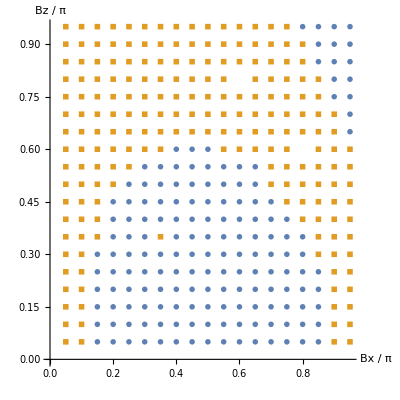

```mathematica
PlotA=ListPlot[{NonDecreasingTracePoints,DecreasingTracePoints},AspectRatio->1,PlotMarkers->{Automatic,0.05},AxesLabel->{"Bx / π","Bz / π"}]
```

```mathematica
TraceListTotalCombined[[31]]
DetListTotalCombined[[31]]
```

{0.1,0.6,{0.379781,0.216352,0.152373,0.117659,0.0958306,0.0808347,0.0699028,0.0615749,0.0550248,0.0497343}}

{0.1,0.6,{97.9518,441.284,1156.3,2339.31,4066.52,6398.6,9350.89,12981.8,17242.1,22195.3}}

```mathematica
TraceListTotalCombined[[137]]
DetListTotalCombined[[137]]
```

{0.4,0.2,{1.04816,2.87795,9.13698,23.6503,53.5731,112.746,226.815,442.301,843.087,1579.37}}

{0.4,0.2,{5.28084,3.26604,1.52763,0.786869,0.433368,0.246187,0.14214,0.0829306,0.0487381,0.0287959}}

```mathematica
TraceListTotalCombined[[225]]
DetListTotalCombined[[225]]
```

{0.6,0.8,{Tr[Inverse[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]],Tr[Inverse[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]],Tr[Inverse[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]],Tr[Inverse[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]],Tr[Inverse[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]],Tr[Inverse[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]],Tr[Inverse[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]],Tr[Inverse[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]],Tr[Inverse[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]],Tr[Inverse[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]]}}

{0.6,0.8,{Det[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}],Det[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}],Det[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}],Det[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}],Det[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]}}

```mathematica
TraceListTotalCombined
```

{{0.1,0.1,{0.131694,0.0682191,0.0466036,0.0357192,0.0292035,0.0248042,0.021741,0.0194497,0.0177279,0.0164105}},{0.1,0.2,{0.141041,0.0733274,0.0502629,0.0385284,0.0313943,0.0265964,0.0231602,0.0205992,0.018639,0.0171072}},{0.1,0.3,{0.158719,0.083891,0.0577994,0.044297,0.0359827,0.0303568,0.0263195,0.023288,0.020925,0.0190365}},{0.1,0.4,{0.191346,0.103529,0.0718002,0.055059,0.0447211,0.0376776,0.0325709,0.0287173,0.0256941,0.0232662}},{0.1,0.5,{0.253416,0.140538,0.0982122,0.0755695,0.0614298,0.0517591,0.0447291,0.0393893,0.0351962,0.0318169}},{0.1,0.6,{0.379781,0.216352,0.152373,0.117659,0.0958306,0.0808347,0.0699028,0.0615749,0.0550248,0.0497343}},{0.1,0.7,{0.68373,0.39836,0.282346,0.218694,0.178461,0.150731,0.130459,0.114994,0.102807,0.0929565}},{0.1,0.8,{1.66041,0.983421,0.699989,0.543391,0.444048,0.375413,0.325156,0.286766,0.256484,0.231986}},{0.1,0.9,{7.86493,4.70045,3.35329,2.60631,2.1315,1.80303,1.56227,1.37824,1.233,1.11545}},{0.2,0.1,{0.372533,0.195034,0.123062,0.129665,0.163268,0.689928,0.38663,0.655527,1.18356,2.13719}},{0.2,0.2,{0.321775,0.14237,0.106829,0.0989457,0.122458,0.141648,0.20082,0.306169,0.49069,0.813372}},{0.2,0.3,{0.27504,0.132783,0.0936281,0.0783588,0.0755074,0.0807435,0.0925742,0.116553,0.155194,0.213569}},{0.2,0.4,{0.280522,0.138511,0.095112,0.0753384,0.0646488,0.0588732,0.0567102,0.0575184,0.0608459,0.0669514}},{0.2,0.5,{0.331008,0.170697,0.117497,0.0909241,0.0749776,0.064397,0.0569614,0.0515972,0.047736,0.0450461}},{0.2,0.6,{0.465261,0.25182,0.175879,0.13594,0.111022,0.0939569,0.0815663,0.0721357,0.0647765,0.0588436}},{0.2,0.7,{0.818349,0.462899,0.32707,0.253295,0.206742,0.17467,0.151232,0.133355,0.119272,0.107892}},{0.2,0.8,{2.04733,1.19558,0.84954,0.658999,0.53828,0.454949,0.393959,0.34739,0.310671,0.280972}},{0.2,0.9,{11.5766,6.87866,4.89846,3.80351,3.10863,2.62843,2.27673,2.00804,1.79608,1.62459}},{0.3,0.1,{1.13489,1.72312,2.66624,22.6341,200.234,273.644,1296.85,8890.76,22406.3,63622.9}},{0.3,0.2,{2.29234,1.96654,1.24389,41.803,10.8439,315.798,202.65,1756.58,5850.48,17718.8}},{0.3,0.3,{12.3326,3.96646,2.38757,6.23542,3.04678,3.7783,9.37601,29.3958,3930.22,239.155}},{0.3,0.4,{7.03687×10^15,3.51844×10^15,-3.51844×10^15,Tr[Inverse[{{5.73707,-4.3028},{-4.3028,3.2271}}]],Tr[Inverse[{{7.71909,-5.78931},{-5.78931,4.34199}}]],-1.75922×10^15,1.75922×10^15,Tr[Inverse[{{14.1694,-10.627},{-10.627,7.97027}}]],8.79609×10^14,-4.39805×10^14}},{0.3,0.5,{0.550787,0.260356,0.174659,0.137402,0.121855,0.116776,0.121927,0.138618,0.166545,0.217143}},{0.3,0.6,{0.646345,0.329107,0.225759,0.174376,0.143392,0.122903,0.108707,0.0985194,0.0910894,0.0859198}},{0.3,0.7,{1.09567,0.600637,0.421511,0.326064,0.266234,0.225139,0.195167,0.172352,0.154415,0.139955}},{0.3,0.8,{2.97981,1.71764,1.2163,0.942057,0.768756,0.649327,0.562036,0.495437,0.442969,0.400551}},{0.3,0.9,{26.9629,15.9077,11.2921,8.75239,7.14522,6.03669,5.2259,4.60711,4.11935,3.72498}},{0.4,0.1,{1.35234,3.15165,5.62571,9.69645,15.7101,24.557,37.4151,55.9418,82.439,120.097}},{0.4,0.2,{1.04816,2.87795,9.13698,23.6503,53.5731,112.746,226.815,442.301,843.087,1579.37}},{0.4,0.3,{4.69125×10^15,2.34562×10^15,-2.34562×10^15,2.34562×10^15,Tr[Inverse[{{4.34199,-5.78931},{-5.78931,7.71909}}]],2.34562×10^15,5.86406×10^14,Tr[Inverse[{{7.97027,-10.627},{-10.627,14.1694}}]],Tr[Inverse[{{9.22038,-12.2938},{-12.2938,16.3918}}]],5.86406×10^14}},{0.4,0.4,{34.7528,11.3959,6.22719,5.31786,63.1705,7.50472,12.2366,33.058,106.671,901.675}},{0.4,0.5,{1.09477,0.487622,0.307837,0.257466,0.257894,0.31049,0.423659,0.632781,1.04509,1.80302}},{0.4,0.6,{0.959343,0.467308,0.318047,0.246584,0.205911,0.180949,0.165635,0.157262,0.15468,0.157638}},{0.4,0.7,{1.71011,0.886626,0.61941,0.478283,0.390371,0.330381,0.286708,0.25353,0.227625,0.206834}},{0.4,0.8,{5.61845,3.21218,2.26402,1.74851,1.42436,1.20156,1.03907,0.915337,0.817933,0.739304}},{0.4,0.9,{315.41,184.512,130.365,100.778,82.1331,69.3089,59.9481,52.8146,47.1981,42.6613}},{0.5,0.1,{10.6052,12.5624,19.6216,28.7411,Tr[Inverse[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]],Tr[Inverse[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]],Tr[Inverse[{{Indeterminate,Indeterminate},{Indeterminate,ComplexInfinity}}]],Tr[Inverse[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]],99.0266,Tr[Inverse[{{Indeterminate,Indeterminate},{Indeterminate,ComplexInfinity}}]]}},{0.5,0.2,{2.21258,4.68082,8.98435,17.7751,32.7254,56.7119,94.4594,153.01,242.79,379.177}},{0.5,0.3,{1.02772,2.46333,13.3287,29.4273,118.656,426.974,1074.17,2740.67,6817.72,16386.3}},{0.5,0.4,{200.887,2.98767,932.537,87.6665,224.958,679.063,459.401,400.903,2940.38,1382.5}},{0.5,0.5,{1.72417,0.634177,0.45337,0.395075,0.422459,0.527073,0.74498,1.15158,1.89435,3.25025}},{0.5,0.6,{1.68988,0.694043,0.477014,0.372012,0.311187,0.274371,0.251847,0.238291,0.232834,0.235666}},{0.5,0.7,{2.96273,1.61461,1.1231,0.864408,0.703216,0.593426,0.513707,0.453292,0.406005,0.367949}},{0.5,0.8,{19.3474,11.0041,7.70202,5.92281,4.81075,4.05,3.4969,3.07671,2.74666,2.48057}},{0.5,0.9,{85.761,49.4607,34.7469,26.7739,21.7751,18.3484,15.8532,13.9553,12.4631,11.2591}},{0.6,0.1,{3.37389,8.39898,18.344,33.7135,57.7087,94.1537,148.666,229.291,347.447,519.282}},{0.6,0.2,{3.0866,6.00731,24.1525,61.9571,144.611,313.774,651.529,1321.04,2630.76,5168.67}},{0.6,0.3,{4.96931,1.97467,24.0719,17.9283,106.347,776.707,1088.44,53517.5,23665.1,234565.}},{0.6,0.4,{6.74619,1.60102,1.09002,1.47266,2.06541,4.38658,8.17422,18.2403,42.1148,94.491}},{0.6,0.5,{1.47084,0.756589,0.534466,0.44936,0.433409,0.4504,0.51015,0.622932,0.788191,1.06452}},{0.6,0.6,{2.35542,1.23816,0.848873,0.654447,0.536894,0.458552,0.403884,0.363224,0.333663,0.310729}},{0.6,0.7,{8.95213,4.88325,3.36968,2.57173,2.07871,1.74425,1.50272,1.32011,1.17713,1.06217}},{0.6,0.8,{Tr[Inverse[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]],Tr[Inverse[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]],Tr[Inverse[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]],Tr[Inverse[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]],Tr[Inverse[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]],Tr[Inverse[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]],Tr[Inverse[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]],Tr[Inverse[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]],Tr[Inverse[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]],Tr[Inverse[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]]}},{0.6,0.9,{12.3417,6.92985,4.84123,3.7199,3.01992,2.54176,2.19442,1.93059,1.72343,1.55652}},{0.7,0.1,{2.4965,7.42577,55.2954,474.21,934.322,2023.23,6619.06,29190.7,158612.,935392.}},{0.7,0.2,{5.23072,16.0029,33.8065,14.5309,30.0848,172.105,8284.54,4261.47,4576.22,13832.9}},{0.7,0.3,{1.63379,5.01135,1.36271,1.75228,2.93648,6.13295,11.134,22.6037,50.3731,108.419}},{0.7,0.4,{1.45578,1.13091,0.661514,0.607255,0.641686,0.725754,0.911037,1.17396,1.61587,2.27584}},{0.7,0.5,{2.45173,1.2532,0.859651,0.663795,0.552504,0.482863,0.435006,0.404518,0.385805,0.374441}},{0.7,0.6,{7.83301,4.07634,2.75292,2.07642,1.6661,1.39107,1.19434,1.04693,0.932395,0.840762}},{0.7,0.7,{539.692,291.373,198.229,149.903,120.422,100.592,86.3507,75.6326,67.2763,60.5797}},{0.7,0.8,{17.6457,9.64185,6.63918,5.05888,4.08476,3.42457,2.94791,2.58777,2.30615,2.07987}},{0.7,0.9,{5.044,2.72402,1.88842,1.45225,1.1817,0.997744,0.864742,0.763943,0.685507,0.622363}},{0.8,0.1,{1.43371,1.00912,1.04532,1.32426,1.90177,2.96467,4.87852,8.31824,14.5183,25.7837}},{0.8,0.2,{1.4994,0.903235,0.78634,0.835531,0.994238,1.2537,1.6631,2.31583,3.36631,5.02853}},{0.8,0.3,{1.93261,0.998809,0.723022,0.615188,0.570563,0.561946,0.584886,0.639402,0.723134,0.835606}},{0.8,0.4,{3.50145,1.69199,1.11397,0.839264,0.680508,0.57794,0.507747,0.458505,0.423428,0.397956}},{0.8,0.5,{12.7669,6.26513,4.07633,3.00116,2.36867,1.95427,1.66253,1.44633,1.27987,1.14789}},{0.8,0.6,{Tr[Inverse[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]],Tr[Inverse[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]],Tr[Inverse[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]],Tr[Inverse[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]],Tr[Inverse[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]],Tr[Inverse[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]],Tr[Inverse[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]],Tr[Inverse[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]],Tr[Inverse[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]],Tr[Inverse[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]]}},{0.8,0.7,{15.617,8.18026,5.52094,4.15833,3.33256,2.77945,2.38345,2.08623,1.85511,1.67034}},{0.8,0.8,{5.13006,2.69773,1.85242,1.41743,1.15465,0.976554,0.849484,0.754966,0.681317,0.623936}},{0.8,0.9,{3.87495,1.72873,1.18919,0.924745,0.775279,0.681852,0.620486,0.585957,0.56905,0.567271}},{0.9,0.1,{3.30204,1.44255,0.888461,0.645181,0.516196,0.440326,0.393182,0.363388,0.345046,0.334864}},{0.9,0.2,{4.93288,2.1082,1.26206,0.884737,0.679504,0.55383,0.470656,0.412578,0.370454,0.339072}},{0.9,0.3,{12.1009,5.20993,3.10912,2.15665,1.63013,1.30194,1.08021,0.921495,0.802867,0.711168}},{0.9,0.4,{157.609,70.8956,43.4142,30.6447,23.4475,18.8882,15.7647,13.5019,11.7923,10.4581}},{0.9,0.5,{50.4034,24.0031,15.2644,11.0606,8.62734,7.05299,5.95579,5.14948,4.53295,4.0468}},{0.9,0.6,{8.81676,4.39016,2.90163,2.16386,1.7253,1.43528,1.2299,1.0775,0.960345,0.867567}},{0.9,0.7,{4.35413,2.238,1.53289,1.17959,0.976588,0.844546,0.753116,0.692213,0.648867,0.619968}},{0.9,0.8,{3.02799,1.75019,1.21227,0.979656,0.874957,0.827717,0.842623,0.894084,1.00139,1.1739}},{0.9,0.9,{4.9209,1.80449,1.36445,1.04813,1.03433,1.16615,1.46882,2.01492,2.9432,4.50605}}}